# Solution Phase Free Energy Surfaces

Constants and Modules

```mathematica
Constants
```

Constants

```mathematica
(* Physical constants in SI units*)
NAvogadro=6.022140857×10^23;
elcharge=1.6021766208×10^-19; (* Elementary charge in C *)
kB=1.38066×10^-23; (* Boltzmann's constant in J K-1 *)
ε0=8.8541878×10^-12; (* Permittivity of free space in C V-1 m-1 *)
n=1.33; (* Optical refractive index of water *)
n0solv=3.33679×10^28; (* Number of water molecules per m3  *) 
R=8.3144598`10; (* Gas constant *)

au2kcal=627.5095`10;

(*Physical constants in au:*)
hbar=1;
hbarps=0.047685388`10/(au2kcal*π);
Dalton=1822.8900409014022`15;
MassH=1.0072756064562605`15;
MassD=2.0135514936645316`15;
MassT=3.0160492`15;
mH=MassH*Dalton;
mD=MassD*Dalton;
mT=MassT*Dalton;
kb=3.16683`10*10^-6;
 
(* Relative permittivity of water *)
εw=78.49; (* for bulk water *)
εCL=2.0; (* in contact layer *) 

(* Faraday's constant: C mol-1 *)
F=96485.33289`10;
```

## Conversion factors

```mathematica
a2m=10^-10;
m2a=10^10;
e2coul=elcharge;
coul2e=1/e2coul;
bohr2a=0.529177`10;
a2bohr=1/bohr2a;
au2kcal=627.5095`10;
kcal2au=1/au2kcal;
ev2cm=8065.54477`10;
cm2ev = 1/ev2cm ;
au2ev=27.2113`10 ;
ev2au = 1/au2ev;
cm2au=cm2ev*ev2au;     
au2cm=1/cm2au;
ev2kcal=ev2au*au2kcal;
kcal2ev=1/ev2kcal;
au2ps=2.4189`10*10^(-5);
ps2au=1/au2ps;
au2fs=au2ps*1000;
fs2au=1/au2fs;
kg2amu=1.660539`10*10^-27;
J2ev=6.2415*10^18;
```

## 1D Morse Potentials

```mathematica
(*
Calculation of Morse beta parameter from vibrational frequency and dissociation energy
*)

(*
ω - vibrational frequency in cm-1;
DE - dissociation energy in kcal mol-1;
μ - reduced mass in amu;
Returns Morse beta parameter in bohr-1
*)

BetaMorse[ω_,DE_,μ_]:=ω cm2au√(μ/(2(DE/au2kcal)));

(*
Energies and wavefunctions for a Morse oscillator
from [J. P. Dahl, M. Springborg, J. Chem. Phys. 88, 4535 (1987)] 
(typo in Eq.(38): factor Sqrt[Alpha] is missing)
*)

(*
Energies of the discrete states
*)

(*
n = 0, 1, 2,... - quantum number;
Beta - Morse parameter (in 1/Bohr);
DE - dissociation energy (in kcal/mol);
M - mass of the particle (in Daltons);
MorseEnergy returns energy in kcal/mol relative to the bottom of the potential well.
*)

MorseEnergy[n_,Beta_,DE_,OptionsPattern[{M->MassH}]]:=Module[{DEA,Lambda,mu},
	DEA=DE*kcal2au;
	mu=OptionValue[M]*Dalton;
	Lambda=Sqrt[2*mu*DEA]/(hbar*Beta);
	au2kcal*hbar*((n+1/2)-1/(2*Lambda)*(n+1/2)^2)*Sqrt[(2*DEA*Beta^2)/mu]
];

(*
Number of bound states in Morse Potential:
Beta - beta parameter (1/Bohr);
DE - dissociation energy (kcal/mol);
M - mass (Daltons).
*)

MorseBound[Beta_,DE_,OptionsPattern[{M->MassH}]]:=Module[{DEA,Lambda,mu},
	DEA=DE*kcal2au;
	mu=OptionValue[M]*Dalton;
	Lambda=Sqrt[2*mu*DEA]/(hbar*Beta);
	IntegerPart[Lambda-1/2]
];
```

```mathematica
(*
Construction of gas phase adiabatic PES for each k-product state along proton coordinate; 0 denotes infinite separation
*)

(*
DE1 - dissociation energy (kcal/mol);
DE2 - dissociation energy (kcal/mol);
Beta1 - beta parameter (1/Bohr);
Beta2 - beta parameter (1/Bohr);
W - coupling parameter between reactor and product diabatic states, in kcal/mol;
Δ - Subscript[ϵ, D]+Subscript[J, DD]-Subscript[ϵ, l], in kcal/mol;
R - distance between donor and acceptor, in Å;
rp - distance from minima of left PES, in Å.
*)


(*
Calculation of Morse beta parameter from vibrational frequency and dissociation energy
*)

(*
ω - vibrational frequency in cm-1;
DE - dissociation energy in kcal mol-1;
μ - reduced mass in amu;
Returns Morse beta parameter in bohr-1
*)

BetaMorse[ω_,DE_,μ_]:=ω cm2au√(μ/(2(DE/au2kcal)));

(*
Energies and wavefunctions for a Morse oscillator
from [J. P. Dahl, M. Springborg, J. Chem. Phys. 88, 4535 (1987)] 
(typo in Eq.(38): factor Sqrt[Alpha] is missing)
*)

(*
Energies of the discrete states
*)

(*
n = 0, 1, 2,... - quantum number;
Beta - Morse parameter (in 1/Bohr);
DE - dissociation energy (in kcal/mol);
M - mass of the particle (in Daltons);
MorseEnergy returns energy in kcal/mol relative to the bottom of the potential well.
*)

MorseEnergy[n_,Beta_,DE_,OptionsPattern[{M->MassH}]]:=Module[{DEA,Lambda,mu},
	DEA=DE*kcal2au;
	mu=OptionValue[M]*Dalton;
	Lambda=Sqrt[2*mu*DEA]/(hbar*Beta);
	au2kcal*hbar*((n+1/2)-1/(2*Lambda)*(n+1/2)^2)*Sqrt[(2*DEA*Beta^2)/mu]
];

(*
Number of bound states in Morse Potential:
Beta - beta parameter (1/Bohr);
DE - dissociation energy (kcal/mol);
M - mass (Daltons).
*)

MorseBound[Beta_,DE_,OptionsPattern[{M->MassH}]]:=Module[{DEA,Lambda,mu},
	DEA=DE*kcal2au;
	mu=OptionValue[M]*Dalton;
	Lambda=Sqrt[2*mu*DEA]/(hbar*Beta);
	IntegerPart[Lambda-1/2]
];


(*
Construction of gas phase adiabatic PES for each k-product state along proton coordinate; 0 denotes infinite separation
*)

(*
DE1 - dissociation energy (kcal/mol);
DE2 - dissociation energy (kcal/mol);
Beta1 - beta parameter (1/Bohr);
Beta2 - beta parameter (1/Bohr);
W - coupling parameter between reactor and product diabatic states, in kcal/mol;
Δ - Subscript[ϵ, D]+Subscript[J, DD]-Subscript[ϵ, l], in kcal/mol;
R - distance between donor and acceptor, in Å;
rp - distance from minima of left PES, in Å.
*)

(*
Morse potential energy curve for donor
*)

MorseLeft[Beta_,DE_,rp_,rDH_]:=Module[{r},
	r=a2bohr*(rp-rDH);
	DE(1-Exp[-Beta*r])^2
];

(*
Morse potential energy curve for acceptor
*)

MorseRight[Beta_,DE_,rp_,rAH_,R_]:=Module[{r},
	r=-1*a2bohr*(rp-R+rAH);
	DE(1-Exp[-Beta*r])^2
];

(*
Adiabatic PES: ground state
*)

AdGS[DE1_,Beta1_,DE2_,Beta2_,rDH_,rAH_,W_,Δ_,R_,rp_,offset_]:=Module[{U1,U2},
U1=MorseLeft[Beta1,DE1,rp,rDH];
U2=MorseRight[Beta2,DE2,rp,rAH,R]+Δ;
N[(U1+U2-Sqrt[(U1-U2)^2+4 W^2])/2+offset]
];
```

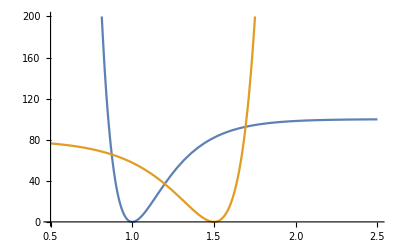

```mathematica
Plot[{MorseLeft[2.5,100,x,1.0],MorseRight[2.0,80,x,1.5,3.0]},{x,0.5,2.5},PlotRange->{0,200}]
```

## Calculation of ψ and concentration of HA as a function of distance from electrode, based on a Modified Gouy-Chapman-Stern Model of the Electrochemical Double Layer

Equations are taken from Bard, A. J. and Fulkner, L. R., Electrochemical Methods: Fundamentals and Applications (2nd Edition), John Wiley & Sons (2001); Relation of ε_OHL to E_OHL from Velikonja, Gongadze, Kralj-Iglic and Iglic, Int. J. Electrochem. Sci. 9, 5885-5894 (2014)

ψs(x), in V vs. potential in bulk liquid

Input parameters:
T -- temperature, in K;
       η -- applied potential, in V vs. E_PZC;
       x1A -- distance of contact layer plane (CLP) from electrode surface, in Å;
       x2A -- distance of outer Helmholtz plane (OHP) from CLP, in Å;
       εI -- relative permittivity (dielectric constant) of contact layer (CL), assumed independent of η;
       ε -- relative permittivity of diffuse layer, assumed independent of η and equal to pure bulk solvent;
       c0ions -- concentration of cations in solution containing only monovalent ions, in M;
       xA -- distance from electrode surface, in Å;

```mathematica
ϕs::badη="The applied potential is anodic of (more positive than) -0.4 V vs. PZC: the ϕOHP expression used here is not valid. Returning Null.";
ϕs[T_,η_,x1A_,x2A_,εI_,ε_,c0ions_,xA_]:=Module[{p0,Langevin,u,n0ions,x1,x2,x,EII,εII,EI,ϕOHP,κ},
If[η>-0.40,Null;Message[ϕs::badη,η],
p0=(√(18 ε0 kB T (εw-n^2)/n0solv))/(2+n^2);
Langevin[u_]=Coth[u]-1/u;
n0ions=c0ions×NAvogadro×1000;
x1=x1A a2m;
x2=x2A a2m;
x=xA a2m;
ϕOHP=(2kB T)/elcharge ArcSinh[√(0.10/c0ions)Sinh[(elcharge (-0.130))/(2kB T)]];
εII[y_]:=n^2+(2+n^2)/(3 y ε0)n0solv p0  Langevin[(((2+n^2)p0 y)/(2 kB T))]; (* note that y here stands for EII below *)
EII=If[η==0,0,
NSolve[{y(x1 εII[y]/εI+x2)==η-ϕOHP},y,Reals]]⟦1,1,2⟧; (* in V/m *)
εII=n^2+(2+n^2)/(3 EII ε0)n0solv p0  Langevin[(((2+n^2)p0 EII)/(2 kB T))];
EI=EII*εII/εI;
κ=elcharge √((2n0ions)/(ε0 ε kB T));
Which[
xA<=x1A,η-x*EI,
x1A<xA<=x1A+x2A,η-x1*EI-(x-x1)EII,
xA>x1A+x2A,1/elcharge 4kB T ArcTanh[Tanh[(elcharge ϕOHP)/(4 kB T)]Exp[-κ(x-x1-x2)]]
]
]
];
```

Work to bring HA from bulk solution to x, in eV

Input parameters:
T -- temperature, in K;
       η -- applied potential, in V vs. E_PZC;
       x1A -- distance of contact layer plane (CLP) from electrode surface, in Å;
       x2A -- distance of outer Helmholtz plane (OHP) from CLP, in Å;
       εI -- relative permittivity (dielectric constant) of contact layer (CL), assumed independent of η;
       ε -- relative permittivity of diffuse layer, assumed independent of η and equal to pure bulk solvent;
       c0ions -- concentration of cations in solution containing only monovalent ions, in M;
       WxminHA -- work term for moving HA from bulk solution to xmin (vide infra), in eV;
       WxminA -- work term for moving A from bulk solution to xmin (vide infra), in eV;
       zHA -- charge of HA;
       xmin -- local concentration maxima of HA closest to electrode surface, in Å;
       khar -- "spring constant" of harmonic PMF for HA in "layer" closest to electrode surface, in kg s^-2 or J m^-2;
       xA -- distance from electrode surface, in Å;

```mathematica
WHAx::badE="The applied potential is anodic of (more positive than) -0.4 V vs. PZC: the ϕOHP expression used here is not valid. Returning Null.";
WHAx[T_,η_,x1A_,x2A_,εI_,ε_,c0ions_,WxminHA_,zHA_,xmin_,khar_,xA_]:=Module[{p0,Langevin,u,n0ions,x1,x2,x,EII,εII,EI,ϕOHP,κ,ϕx,WtotHA},
If[η>-0.40,Null;Message[ϕs::badη,η],
p0=(√(18 ε0 kB T (εw-n^2)/n0solv))/(2+n^2);
Langevin[u_]=Coth[u]-1/u;
n0ions=c0ions×NAvogadro×1000;
x1=x1A a2m;
x2=x2A a2m;
x=xA a2m;
ϕOHP=(2kB T)/elcharge ArcSinh[√(0.10/c0ions)Sinh[(elcharge (-0.130))/(2kB T)]];
εII[y_]:=n^2+(2+n^2)/(3 y ε0)n0solv p0  Langevin[(((2+n^2)p0 y)/(2 kB T))]; (* note that y here stands for EII below *)
EII=If[η==0,0,
NSolve[{y(x1 εII[y]/εI+x2)==η-ϕOHP},y,Reals]]⟦1,1,2⟧; (* in V/m *)
εII=n^2+(2+n^2)/(3 EII ε0)n0solv p0  Langevin[(((2+n^2)p0 EII)/(2 kB T))];
EI=EII*εII/εI;
κ=elcharge √((2n0ions)/(ε0 ε kB T));
ϕx=Which[
xA<=x1A,η-x*EI,
x1A<xA<=x1A+x2A,η-x1*EI-(x-x1)EII,
xA>x1A+x2A,1/elcharge 4kB T ArcTanh[Tanh[(elcharge ϕOHP)/(4 kB T)]Exp[-κ(x-x1-x2)]]
];
zHA*ϕx+WxminHA+(khar*(x-xmin*a2m)^2*J2ev)/2 
(* total work term, electrostatic and non-electrostatic, for HA at x, in eV *)

]
];
```

Concentration of HA at x

Input parameters:
T -- temperature, in K;
       η -- applied potential, in V vs. E_PZC;
       x1A -- distance of contact layer plane (CLP) from electrode surface, in Å;
       x2A -- distance of outer Helmholtz plane (OHP) from CLP, in Å;
       εI -- relative permittivity (dielectric constant) of contact layer (CL), assumed independent of η;
       ε -- relative permittivity of diffuse layer, assumed independent of η and equal to pure bulk solvent;
       c0ions -- concentration of cations in solution containing only monovalent ions, in M;
       WxminHA -- work term for moving HA from bulk solution to xmin (vide infra), in eV;
       WxminA -- work term for moving A from bulk solution to xmin (vide infra), in eV;
       zHA -- charge of HA;
       xmin -- local concentration maxima of HA closest to electrode surface, in Å;
       khar -- "spring constant" of harmonic PMF for HA in "layer" closest to electrode surface, in kg s^-2 or J m^-2;
       cHA -- bulk concentration of HA;
     xA -- distance from electrode surface, in Å;

```mathematica
cHAx::badη="The applied potential is anodic of (more positive than) -0.4 V vs. PZC: the ϕOHP expression used here is not valid. Returning Null.";
cHAx[T_,η_,x1A_,x2A_,εI_,ε_,c0ions_,WxminHA_,zHA_,xmin_,khar_,cHA_,xA_]:=Module[{p0,Langevin,u,n0ions,x1,x2,x,EII,εII,EI,ϕOHP,κ,ϕx,WtotHA},
If[η>-0.40,Null;Message[ϕs::badη,η],
p0=(√(18 ε0 kB T (εw-n^2)/n0solv))/(2+n^2);
Langevin[u_]=Coth[u]-1/u;
n0ions=c0ions×NAvogadro×1000;
x1=x1A a2m;
x2=x2A a2m;
x=xA a2m;
ϕOHP=(2kB T)/elcharge ArcSinh[√(0.10/c0ions)Sinh[(elcharge (-0.130))/(2kB T)]];
εII[y_]:=n^2+(2+n^2)/(3 y ε0)n0solv p0  Langevin[(((2+n^2)p0 y)/(2 kB T))]; (* note that y here stands for EII below *)
EII=If[η==0,0,
NSolve[{y(x1 εII[y]/εI+x2)==η-ϕOHP},y,Reals]]⟦1,1,2⟧; (* in V/m *)
εII=n^2+(2+n^2)/(3 EII ε0)n0solv p0  Langevin[(((2+n^2)p0 EII)/(2 kB T))];
EI=EII*εII/εI;
κ=elcharge √((2n0ions)/(ε0 ε kB T));
ϕx=Which[
xA<=x1A,η-x*EI,
x1A<xA<=x1A+x2A,η-x1*EI-(x-x1)EII,
xA>x1A+x2A,1/elcharge 4kB T ArcTanh[Tanh[(elcharge ϕOHP)/(4 kB T)]Exp[-κ(x-x1-x2)]]
];
WtotHA=zHA*ϕx+WxminHA+(khar*(x-xmin*a2m)^2*J2ev)/2; (* total work term, electrostatic and non-electrostatic, for HA at x, in eV *)
cHA*Exp[-WtotHA*ev2au/kb/T]
]
];
```

## Solution Phase FES Incorporating Effects of Applied Potential and EDL

```mathematica
Integrate[1/π(γ/2)/(γ^2/4+(ϵ-ϵc)^2)1/(ϵ+dG),{ϵ,-∞,0},Assumptions->{γ>0,ϵc∈Reals,dG∈Reals},PrincipalValue->True]
```

ConditionalExpression[(2 (dG+ϵc) (π-2 ArcTan[(2 ϵc)/γ])+γ Log[(4 dG^2)/(γ^2+4 ϵc^2)])/(π (γ^2+4 (dG+ϵc)^2)),dG≤0]

```mathematica
ΔGG[ΔGkF_,W_,ϵc_,γ_]:=Module[{Δ},Re@FindRoot[Δ+W^2((Δ-ΔGkF+ϵc) (π-2 ArcTan[ϵc/γ])+γ Log[(Δ-ΔGkF)^2/(γ^2+ϵc^2)])/(2 π (γ^2+(Δ-ΔGkF+ϵc)^2)),{Δ,0},WorkingPrecision->100,MaxIterations->1000][[1,2]]];
```

```mathematica
ΔGG[10,100,0,200]
```

31.99613422958936734718233170449302320501622181682556223334013904280956943209507536114175720278894477

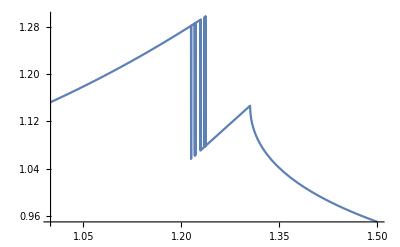

```mathematica
Plot[{ΔGG[ΔGkF,10,-10,200]},{ΔGkF,1,1.5},PlotRange->All]
```

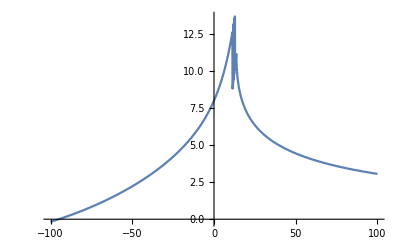

```mathematica
Plot[{ΔGG[ΔGkF,40,0,200]},{ΔGkF,-100,100},PlotRange->All]
```

```mathematica
(2 (dG+ϵc) (π-2 ArcTan[(2 ϵc)/γ])+γ Log[(4 dG^2)/(γ^2+4 ϵc^2)])/(π (γ^2+4 (dG+ϵc)^2))
```

```mathematica
ΔGGa[ΔGG_,ΔGkF_,W_,ϵc_,γ_]:=W^2((ΔGG-ΔGkF+ϵc) (π-2 ArcTan[ϵc/γ])+γ Log[(ΔGG-ΔGkF)^2/(γ^2+ϵc^2)])/(2 π (γ^2+(ΔGG-ΔGkF+ϵc)^2));
ΔGGa1[dG_,ΔGkF_,W_,ϵc_,γ_]:=(2 (dG+ϵc) (π-2 ArcTan[(2 ϵc)/γ])+γ Log[(4 dG^2)/(γ^2+4 ϵc^2)])/(π (γ^2+4 (dG+ϵc)^2));
ΔGGa2[dG_,ΔGkF_,W_,ϵc_,γ_]:=-(2 dG π-2 π ϵc+4 (-dG+ϵc) ArcTan[(2 ϵc)/γ]-γ Log[4]+γ Log[(γ^2+4 ϵc^2)/dG^2])/(π (γ^2+4 (dG-ϵc)^2));
```

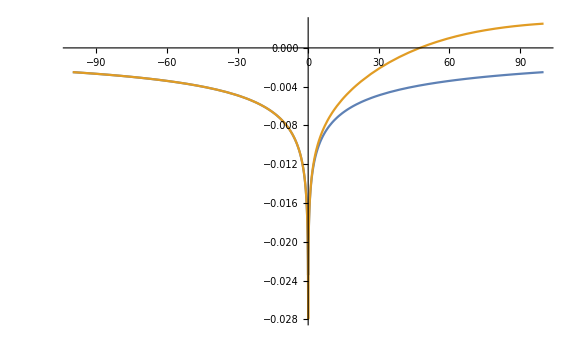

```mathematica
Plot[{If[ΔGG≤0,ΔGGa1[ΔGG,0,10,0,200],ΔGGa2[ΔGG,0,10,0,200]],ΔGGa1[ΔGG,0,10,0,200]},{ΔGG,-100,100},PlotRange->All,ImageSize->Large]
```

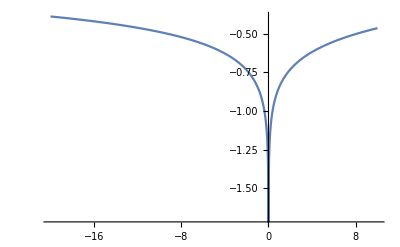

```mathematica
Plot[{ΔGGa[ΔGG,0,10,0,200]},{ΔGG,-20,10},PlotRange->All]
```

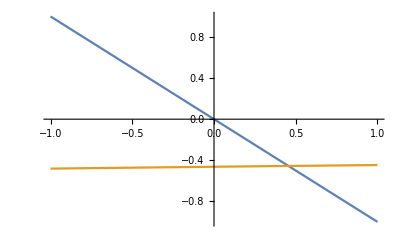

```mathematica
Plot[{-ΔGG,ΔGGa[ΔGG,-10,10,0,200]},{ΔGG,-1,1}]
```

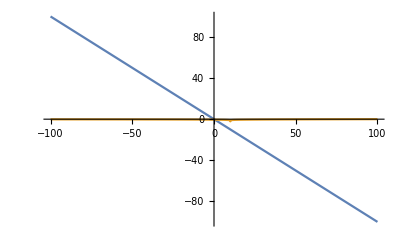

```mathematica
Plot[{-ΔGG,ΔGGa[ΔGG,10,10,0,200]},{ΔGG,-100,100}]
```

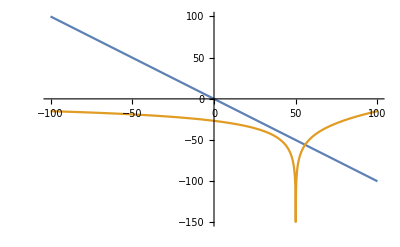

```mathematica
Plot[{-ΔGG,ΔGGa[ΔGG,50,100,0,200]},{ΔGG,-100,100}]
```

```mathematica
SolGSFermiFixedR[DE1_,ω1_,DE2_,ω2_,rDH_,rAH_,W_,ΔkF_,X_,λ_,Δs_,T_,x1A_,x2A_,εI_,ε_,c0ions_,xA_,χs_,WxminHA_,zHA_,xmin_,khar_,R_,E_,rp_]:=Module[{Beta1,Beta2,U1gas,ΔUgaskF,G1,ϕsx,ΔGelst,ΔGkF,G2},
Beta1=BetaMorse[ω1,DE1,mH];
Beta2=BetaMorse[ω2,DE2,mH];
U1gas=MorseLeft[Beta1,DE1,rp,rDH];
ΔUgaskF=MorseRight[Beta2,DE2,rp,rAH,R]+ΔkF-U1gas;
ϕsx=ϕs[T,E,x1A,x2A,εI,ε,c0ions,xA];(* Print["ϕsx: ",ϕsx]; *)
ΔGelst=ev2kcal(E+χs-ϕsx);(* Print["ΔGelst: ",ΔGelst]; *)
G1=U1gas+(X+λ)^2/4/λ+(ϕsx+WxminHA+(khar*((xA-xmin)*a2m)^2*J2ev)/2 )ev2kcal; 
(* Print["G^R: ",G1]; *)
ΔGkF=ΔUgaskF+X+ΔGelst; 
(* Print["ΔGkF: ",ΔGkF]; *)
G2=G1+ΔGkF;
N[(G1+G2-Sqrt[(G1-G2)^2+4 W^2])/2]
];
```

```mathematica
DE1A=100;ω1A=3500;DE2A=52.14;ω2A=1880;rDH=0.976;rAH=1.60;WA=10;λA=10.0;
ΔGelstA=-20;ΔsA1=20;ΔkA1=-30;ϵcA=-230 (* -10 eV *); γA=100;TT=298;xCL=3.2;xOHL=3.5;εCL=2;
c0ionsA=0.10;xAA=RA;RA=3.10;χsA=0;offset=0;
```

```mathematica
δRA=0.1;
zH3O=1;
WxminHA=0.3;
kharA=15;
```

```mathematica
SolGSFermiFixedR[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,15,0,λA,ΔsA1,TT,xCL,xOHL,εCL,εw,c0ionsA,RA,χsA,WxminHA,zH3O,xCL,kharA,2.9,-1.0,1.0]
```

-2.48478

```mathematica
SolGSFermiFixedR[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,15,0,λA,ΔsA1,TT,xCL,xOHL,εCL,εw,c0ionsA,RA,χsA,WxminHA,zH3O,xCL,kharA,2.9,-1.0,1.15]
```

ΔGkF: -12.0403

-1.54093

```mathematica
SolGSFermiFixedR[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,15,0,λA,ΔsA1,TT,xCL,xOHL,εCL,εw,c0ionsA,RA,χsA,WxminHA,zH3O,xCL,kharA,2.9,-1.0,1.3]
```

ΔGkF: -31.3014

-1.45646

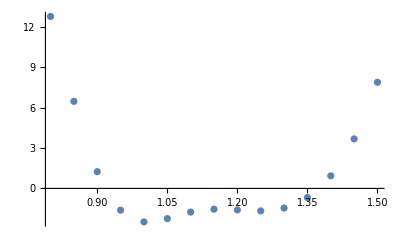

```mathematica
ListPlot[Table[{rp,SolGSFermiFixedR[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,15,0,λA,ΔsA1,TT,xCL,xOHL,εCL,εw,c0ionsA,RA,χsA,WxminHA,zH3O,xCL,kharA,2.9,-1.0,rp]},{rp,0.8,1.5,0.05}]]
```

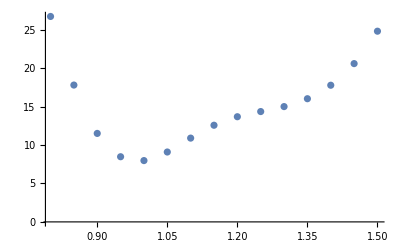

```mathematica
ListPlot[Table[{rp,SolGSFermiFixedR[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,15,10,λA,ΔsA1,TT,xCL,xOHL,εCL,εw,c0ionsA,RA,χsA,WxminHA,zH3O,xCL,kharA,2.9,-1.0,rp]},{rp,0.8,1.5,0.05}]]
```

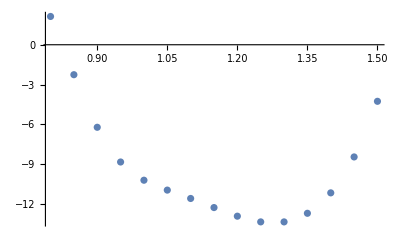

```mathematica
ListPlot[Table[{rp,SolGSFermiFixedR[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,15,-10,λA,ΔsA1,TT,xCL,xOHL,εCL,εw,c0ionsA,RA,χsA,WxminHA,zH3O,xCL,kharA,2.9,-1.0,rp]},{rp,0.8,1.5,0.05}]]
```

Construction of Solution Phase FES at each R, as functions of Proton Coordinate rp and Collective Solvent Coordinate X  

Input parameters:
   DE1 - dissociation energy (kcal/mol);
	DE2 - dissociation energy (kcal/mol);
	ω1 - vibrational frequency (cm-1);
	ω2- beta parameter (cm-1);
	W - coupling parameter between reactor and product diabatic states, in kcal/mol; 
	ΔkF - intrinsic bias, ϵ_D+J_DD-ϵ_kF+const., in kcal/mol;
	X - diabatic solvation energy gap, in kcal/mol; 
	λ - solvent reorganization energy, in kcal/mol; 
	Δs - difference in equilibrium solvation energy, in kcal/mol;
	ϵc - center of band relative to Fermi level, in kcal/mol; 
	γ - parameter equal to half FWHM in Cauchy-Lorentzian DOS distribution, in kcal/mol; 
	T -- temperature, in K; 
	x1A -- distance of contact layer plane (CLP) from electrode surface,in Å;
	x2A -- distance of outer Helmholtz plane (OHP) from CLP, in Å
	εI -- relative permittivity (dielectric constant) of contact layer (CL), assumed independent of η;
	ε -- relative permittivity of diffuse layer, assumed independent of E and equal to pure bulk solvent; 
	c0ions -- concentration of cations in solution containing only monovalent ions, in M;
             WxminHA -- work term for moving HA from bulk solution to xmin (vide infra), in eV;
             WxminA -- work term for moving A from bulk solution to xmin (vide infra), in eV;
             zHA -- charge of HA;
            xmin -- local concentration maxima of HA closest to electrode surface, in Å;
             khar -- "spring constant" of harmonic PMF for HA in "layer" closest to electrode surface, in kg s^-2 or J m^-2;
	xA -- distance from electrode surface, in Å, usually set equal to R;
	R - distance between donor and acceptor, in Å; 
	E-- applied potential, in V vs. E_PZC; 
	rp - distance from minima of left PES, in Å.

Select local variables:
       rp - distance from minima of left PES, in Å;
	G1 - solution phase free energy of reactant state, in kcal/mol;
	ΔGelst -  reaction free energy contribution of electric field, in kcal/mol;
	ΔGkF - Volmer reaction free energy for reaction involving an electron at Fermi level, in kcal/mol;
	ΔGG - Volmer reaction free energy considering all filled bands, in kcal/mol;

Ground-state solution-phase FES at fixed R and E: Cauchy-Lorentzian distribution used to model DOS; EDL effects incorporated into reactant and product diabatic FESes

```mathematica
SolGSCauchyFixedR[DE1_,ω1_,DE2_,ω2_,rDH_,rAH_,W_,ΔkF_,X_,λ_,Δs_,ϵc_,γ_,T_,x1A_,x2A_,εI_,ε_,c0ions_,xA_,χs_,WxminHA_,zHA_,xmin_,khar_,R_,E_,rp_]:=Module[{Beta1,Beta2,U1gas,ΔUgaskF,G1,ϕsx,ΔGelst,ΔGkF,ΔGG},
Beta1=BetaMorse[ω1,DE1,mH];
Beta2=BetaMorse[ω2,DE2,mH];
U1gas=MorseLeft[Beta1,DE1,rp,rDH];
ΔUgaskF=MorseRight[Beta2,DE2,rp,rAH,R]+ΔkF-U1gas;
ϕsx=ϕs[T,E,x1A,x2A,εI,ε,c0ions,xA];(* Print["ϕsx: ",ϕsx]; *)
G1=U1gas+(X+λ-Δs)^2/4/λ+(ϕsx+WxminHA+(khar*((xA-xmin)*a2m)^2*J2ev)/2 )ev2kcal; 
(* Print["G^R: ",G1]; *)
ΔGelst=ev2kcal(E+χs-ϕsx);(* Print["ΔGelst: ",ΔGelst]; *)
ΔGkF=ΔUgaskF+X+ΔGelst;(* Print["ΔGkF: ",ΔGkF]; *)
ΔGG=Re@FindRoot[ΔGG+W^2((ΔGG-ΔGkF+ϵc) (π-2 ArcTan[ϵc/γ])+γ Log[(ΔGG-ΔGkF)^2/(γ^2+ϵc^2)])/(2 π (γ^2+(ΔGG-ΔGkF+ϵc)^2))==0,{ΔGG,0},WorkingPrecision->100,MaxIterations->1000][[1,2]]; (* Print["ΔGG: ",ΔGG]; *)
ΔGG+G1
];
```

```mathematica
SolGSCauchyFixedRMod[DE1_,ω1_,DE2_,ω2_,rDH_,rAH_,W_,ΔkF_,X_,λ_,Δs_,ϵc_,γ_,T_,x1A_,x2A_,εI_,ε_,c0ions_,xA_,χs_,WxminHA_,zHA_,xmin_,khar_,R_,E_,rp_]:=Module[{Beta1,Beta2,U1gas,ΔUgaskF,G1,ϕsx,ΔGelst,ΔGkF,ΔGG},
Beta1=BetaMorse[ω1,DE1,mH];
Beta2=BetaMorse[ω2,DE2,mH];
U1gas=MorseLeft[Beta1,DE1,rp,rDH];
ΔUgaskF=MorseRight[Beta2,DE2,rp,rAH,R]+ΔkF-U1gas;
ϕsx=ϕs[T,E,x1A,x2A,εI,ε,c0ions,xA];(* Print["ϕsx: ",ϕsx]; *)
ΔGelst=ev2kcal(E+χs-ϕsx);(* Print["ΔGelst: ",ΔGelst]; *)
G1=U1gas+(X+λ)^2/4/λ+(ϕsx+WxminHA+(khar*((xA-xmin)*a2m)^2*J2ev)/2 )ev2kcal; 
(* Print["G^R: ",G1]; *)
ΔGkF=ΔUgaskF+X+ΔGelst; (*Print["ΔGkF: ",ΔGkF]; *)
ΔGG=Re@FindRoot[ΔGG+W^2((ΔGG-ΔGkF+ϵc) (π-2 ArcTan[ϵc/γ])+γ Log[(ΔGG-ΔGkF)^2/(γ^2+ϵc^2)])/(2 π (γ^2+(ΔGG-ΔGkF+ϵc)^2))==0,{ΔGG,0},WorkingPrecision->1000,MaxIterations->1000][[1,2]]; (* Print["ΔGG: ",ΔGG]; *)
ΔGG+G1
];
```

```mathematica
SolGSCauchyFixedRMod[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkA1,10,λA,ΔsA1,ϵcA,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,RA,χsA,WxminHA,zH3O,xCL,kharA,RA,-1.0,1.0]
```

13.6409

```mathematica
SolGSCauchyFixedRMod[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkA1,-10,λA,ΔsA1,ϵcA,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,RA,χsA,WxminHA,zH3O,xCL,kharA,RA,-1.0,1.0]
```

3.64241

```mathematica
RB=2.8;
```

```mathematica
SolGSCauchyFixedRMod[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkA1,10,λA,ΔsA1,ϵcA,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,RB,χsA,WxminHA,zH3O,xCL,kharA,RB,-1.0,1.0]
```

G^R: 2.94593

ΔGkF: -33.023

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

ΔGG: -33.023

-30.0771

```mathematica
SolGSCauchyFixedRMod[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkA1,-10,λA,ΔsA1,ϵcA,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,RB,χsA,WxminHA,zH3O,xCL,kharA,RB,-1.0,1.0]
```

G^R: 12.9459

ΔGkF: -53.023

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

ΔGG: -53.023

-40.0771

```mathematica
SolGSCauchyFixedRMod[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkA1,-10,λA,ΔsA1,ϵcA,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,RB,χsA,WxminHA,zH3O,xCL,kharA,RB,-1.0,1.3]
```

G^R: 40.0566

ΔGkF: -82.678

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

ΔGG: -82.678

-42.6214

```mathematica
RC=2.9;
```

```mathematica
SolGSCauchyFixedRMod[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkA1,10,λA,ΔsA1,ϵcA,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,RC,χsA,WxminHA,zH3O,xCL,kharA,RC,-1.0,1.0]
```

G^R: 2.80013

ΔGkF: -29.6378

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

ΔGG: -29.6378

-26.8377

```mathematica
SolGSCauchyFixedRMod[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkA1,10,λA,ΔsA1,ϵcA,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,RC,χsA,WxminHA,zH3O,xCL,kharA,RC,-1.0,1.25]
```

G^R: 24.1993

ΔGkF: -59.0234

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

ΔGG: -59.0234

-34.8241

```mathematica
SolGSCauchyFixedRMod[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkA1,10,λA,ΔsA1,ϵcA,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,RC,χsA,WxminHA,zH3O,xCL,kharA,RC,-1.0,1.5]
```

G^R: 51.2877

ΔGkF: -77.8905

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

ΔGG: -77.8905

-26.6027

```mathematica
SolGSCauchyFixedRMod[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkA1,-10,λA,ΔsA1,ϵcA,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,RC,χsA,WxminHA,zH3O,xCL,kharA,RC,-1.0,1.0]
```

G^R: 12.8001

ΔGkF: -49.6378

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

ΔGG: -49.6378

-36.8377

```mathematica
SolGSCauchyFixedRMod[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkA1,-10,λA,ΔsA1,ϵcA,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,RC,χsA,WxminHA,zH3O,xCL,kharA,RC,-1.0,1.5]
```

G^R: 61.2877

ΔGkF: -97.8905

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

ΔGG: -97.8905

-36.6027

```mathematica
ΔkA1=-500
```

-500

```mathematica
ϵcA1=0
```

0

FindRoot::precw: The precision of the argument function (ΔGG$27788+(50 (π (498.209+ΔGG$27788)+100 Log[Power[«2»]/10000]))/(π (10000+(498.209+ΔGG$27788)^2))==0) is less than WorkingPrecision (1000.).

FindRoot::precw: The precision of the argument function (ΔGG$27802+(50 (π (486.719+ΔGG$27802)+100 Log[Power[«2»]/10000]))/(π (10000+(486.719+ΔGG$27802)^2))==0) is less than WorkingPrecision (1000.).

FindRoot::precw: The precision of the argument function (ΔGG$27816+(50 (π (481.171+ΔGG$27816)+100 Log[Power[«2»]/10000]))/(π (10000+(481.171+ΔGG$27816)^2))==0) is less than WorkingPrecision (1000.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

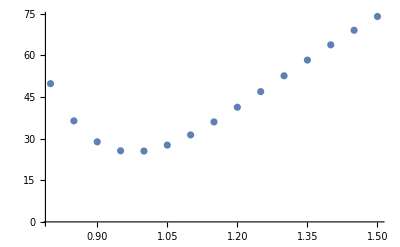

```mathematica
ListPlot[Table[{rp,SolGSCauchyFixedRMod[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkA1,20,λA,ΔsA1,ϵcA1,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,RA,χsA,WxminHA,zH3O,xCL,kharA,RA,-1.0,rp]},{rp,0.8,1.5,0.05}]]
```

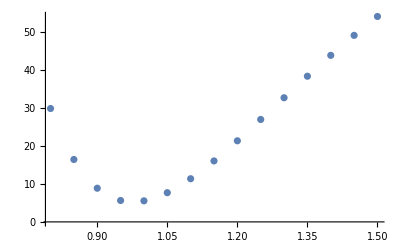

```mathematica
ListPlot[Table[{rp,SolGSCauchyFixedRMod[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkA1,0,λA,ΔsA1,ϵcA1,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,RA,χsA,WxminHA,zH3O,xCL,kharA,RA,-1.0,rp]},{rp,0.8,1.5,0.05}]]
```

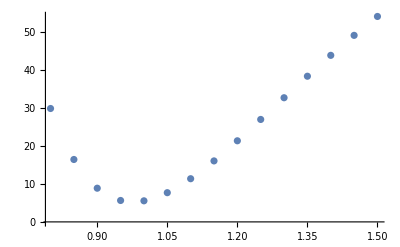

```mathematica
ListPlot[Table[{rp,SolGSCauchyFixedRMod[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkA1,-20,λA,ΔsA1,ϵcA1,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,RA,χsA,WxminHA,zH3O,xCL,kharA,RA,-1.0,rp]},{rp,0.8,1.5,0.05}]]
```

FindRoot::precw: The precision of the argument function (ΔGG$29067+(5000 (π (-31.7906+ΔGG$29067)+100 Log[Power[«2»]/10000]))/(π (10000+(-31.7906+ΔGG$29067)^2))==0) is less than WorkingPrecision (1000.).

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 1000. digits of working precision to meet these tolerances.

FindRoot::precw: The precision of the argument function (ΔGG$29085+(5000 (π (-43.2808+ΔGG$29085)+100 Log[Power[«2»]/10000]))/(π (10000+(-43.2808+ΔGG$29085)^2))==0) is less than WorkingPrecision (1000.).

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 1000. digits of working precision to meet these tolerances.

FindRoot::precw: The precision of the argument function (ΔGG$29105+(5000 (π (-48.8286+ΔGG$29105)+100 Log[Power[«2»]/10000]))/(π (10000+(-48.8286+ΔGG$29105)^2))==0) is less than WorkingPrecision (1000.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 1000. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

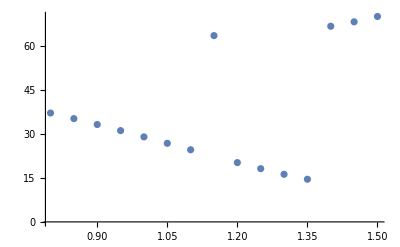

```mathematica
ListPlot[Table[{rp,SolGSCauchyFixedRMod[DE1A,ω1A,DE2A,ω2A,rDH,rAH,100,50,0,λA,ΔsA1,ϵcA1,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,RA,χsA,WxminHA,zH3O,xCL,kharA,RA,-1.0,rp]},{rp,0.8,1.5,0.05}]]
```

```mathematica
ΔkA2=20
```

20

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

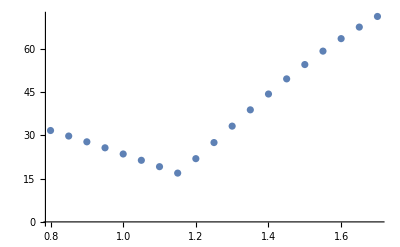

```mathematica
ListPlot[Table[{rp,SolGSCauchyFixedRMod1A[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkA2,0,λA,ΔsA1,ϵcA,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,RA,χsA,WxminHA,zH3O,xCL,kharA,RA,-1.0,rp]},{rp,0.8,1.7,0.05}]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {ΔGG$37887} = {8.82861}.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

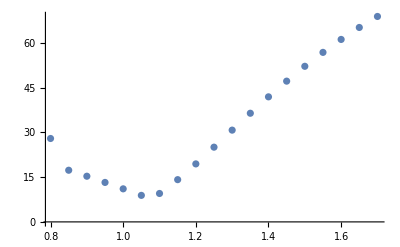

```mathematica
ListPlot[Table[{rp,SolGSCauchyFixedRMod1A[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkA2,-10,λA,ΔsA1,ϵcA,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,RA,χsA,WxminHA,zH3O,xCL,kharA,RA,-1.0,rp]},{rp,0.8,1.7,0.05}]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

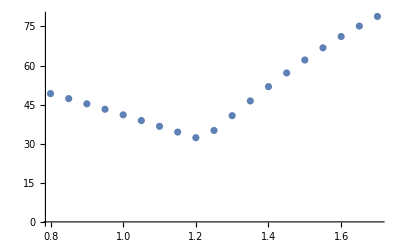

```mathematica
ListPlot[Table[{rp,SolGSCauchyFixedRMod1A[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkA2,10,λA,ΔsA1,ϵcA,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,RA,χsA,WxminHA,zH3O,xCL,kharA,RA,-1.0,rp]},{rp,0.8,1.7,0.05}]]
```

```mathematica
ΔkA3=40
```

40

G^R: 29.4225

ΔGkF: 21.7906

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

ΔGG: 21.7906

G^R: 16.0114

ΔGkF: 33.2808

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

ΔGG: 33.2808

G^R: 8.45838

ΔGkF: 38.8286

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

ΔGG: 38.8286

G^R: 5.22901

ΔGkF: 39.9771

ΔGG: 39.9771

G^R: 5.13888

ΔGkF: 37.923

ΔGG: 37.923

G^R: 7.27824

ΔGkF: 33.5929

ΔGG: 33.5929

G^R: 10.9523

ΔGkF: 27.704

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

ΔGG: 27.704

G^R: 15.6341

ΔGkF: 20.8129

ΔGG: 20.8129

G^R: 20.9276

ΔGkF: 13.3537

ΔGG: 13.3537

G^R: 26.5381

ΔGkF: 5.66937

ΔGG: 5.66937

G^R: 32.2496

ΔGkF: -1.96329

ΔGG: 0.557451

G^R: 37.9065

ΔGkF: -9.31264

ΔGG: 0.503739

G^R: 43.3997

ΔGkF: -16.1751

ΔGG: 0.489606

G^R: 48.6554

ΔGkF: -22.3605

ΔGG: 0.484522

G^R: 53.6265

ΔGkF: -27.6783

ΔGG: 0.48305

G^R: 58.2856

ΔGkF: -31.9263

ΔGG: 0.483113

G^R: 62.6206

ΔGkF: -34.8786

ΔGG: 0.48364

G^R: 66.6297

ΔGkF: -36.2737

ΔGG: 0.484004

G^R: 70.3191

ΔGkF: -35.8028

ΔGG: 0.483874

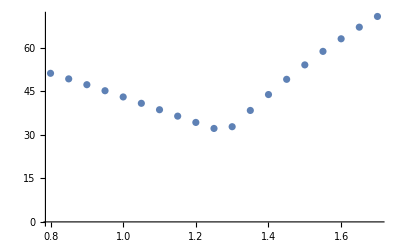

```mathematica
ListPlot[Table[{rp,SolGSCauchyFixedRMod1A[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkA3,0,λA,ΔsA1,ϵcA,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,RA,χsA,WxminHA,zH3O,xCL,kharA,RA,-1.0,rp]},{rp,0.8,1.7,0.05}]]
```

G^R: 30.5171

ΔGkF: 21.7906

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

ΔGG: 21.7906

G^R: 17.106

ΔGkF: 33.2808

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

ΔGG: 33.2808

G^R: 9.55299

ΔGkF: 38.8286

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

ΔGG: 38.8286

G^R: 6.32363

ΔGkF: 39.9771

ΔGG: 39.9771

G^R: 6.2335

ΔGkF: 37.923

ΔGG: 37.923

G^R: 8.37285

ΔGkF: 33.5929

ΔGG: 33.5929

G^R: 12.0469

ΔGkF: 27.704

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

ΔGG: 27.704

G^R: 16.7287

ΔGkF: 20.8129

ΔGG: 20.8129

G^R: 22.0222

ΔGkF: 13.3537

ΔGG: 13.3537

G^R: 27.6327

ΔGkF: 5.66937

ΔGG: 5.66937

G^R: 33.3442

ΔGkF: -1.96329

ΔGG: 0.557451

G^R: 39.0011

ΔGkF: -9.31264

ΔGG: 0.503739

G^R: 44.4944

ΔGkF: -16.1751

ΔGG: 0.489606

G^R: 49.7501

ΔGkF: -22.3605

ΔGG: 0.484522

G^R: 54.7211

ΔGkF: -27.6783

ΔGG: 0.48305

G^R: 59.3803

ΔGkF: -31.9263

ΔGG: 0.483113

G^R: 63.7152

ΔGkF: -34.8786

ΔGG: 0.48364

G^R: 67.7243

ΔGkF: -36.2737

ΔGG: 0.484004

G^R: 71.4137

ΔGkF: -35.8028

ΔGG: 0.483874

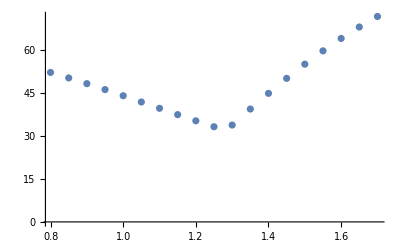

```mathematica
ListPlot[Table[{rp,SolGSCauchyFixedRMod1A[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkA3,-20,λA,ΔsA1,ϵcA,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,RA,χsA,WxminHA,zH3O,xCL,kharA,RA,-1.0,rp]},{rp,0.8,1.7,0.05}]]
```

G^R: 38.5644

ΔGkF: -8.20937

ΔGG: 0.507625

G^R: 25.1533

ΔGkF: 3.28079

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

ΔGG: 3.28079

G^R: 17.6003

ΔGkF: 8.82861

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {ΔGG$19151} = {8.82861}.

ΔGG: 8.82861

G^R: 14.3709

ΔGkF: 9.97714

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

ΔGG: 9.97714

G^R: 14.2808

ΔGkF: 7.92301

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

ΔGG: 7.92301

G^R: 16.4202

ΔGkF: 3.59286

ΔGG: 3.59286

G^R: 20.0942

ΔGkF: -2.29597

ΔGG: 0.552028

G^R: 24.776

ΔGkF: -9.18705

ΔGG: 0.504148

G^R: 30.0695

ΔGkF: -16.6463

ΔGG: 0.48904

G^R: 35.68

ΔGkF: -24.3306

ΔGG: 0.483735

G^R: 41.3915

ΔGkF: -31.9633

ΔGG: 0.483117

G^R: 47.0484

ΔGkF: -39.3126

ΔGG: 0.485021

G^R: 52.5417

ΔGkF: -46.1751

ΔGG: 0.488239

G^R: 57.7974

ΔGkF: -52.3605

ΔGG: 0.491979

G^R: 62.7684

ΔGkF: -57.6783

ΔGG: 0.495662

G^R: 67.4276

ΔGkF: -61.9263

ΔGG: 0.498841

G^R: 71.7625

ΔGkF: -64.8786

ΔGG: 0.501146

G^R: 75.7716

ΔGkF: -66.2737

ΔGG: 0.502258

G^R: 79.461

ΔGkF: -65.8028

ΔGG: 0.501881

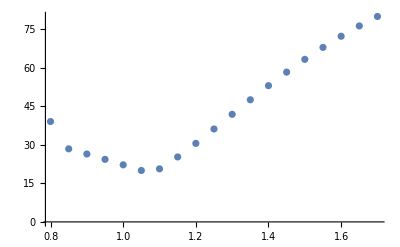

```mathematica
ListPlot[Table[{rp,SolGSCauchyFixedRMod1A[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkA2,-30,λA,ΔsA1,ϵcA,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,RA,χsA,WxminHA,zH3O,xCL,kharA,RA,-1.0,rp]},{rp,0.8,1.7,0.05}]]
```

G^R: 36.3752

ΔGkF: 31.7906

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

ΔGG: 31.7906

G^R: 22.964

ΔGkF: 43.2808

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

ΔGG: 43.2808

G^R: 15.4111

ΔGkF: 48.8286

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

ΔGG: 48.8286

G^R: 12.1817

ΔGkF: 49.9771

ΔGG: 49.9771

G^R: 12.0916

ΔGkF: 47.923

ΔGG: 47.923

G^R: 14.2309

ΔGkF: 43.5929

ΔGG: 43.5929

G^R: 17.905

ΔGkF: 37.704

ΔGG: 37.704

G^R: 22.5868

ΔGkF: 30.8129

ΔGG: 30.8129

G^R: 27.8803

ΔGkF: 23.3537

ΔGG: 23.3537

G^R: 33.4908

ΔGkF: 15.6694

ΔGG: 15.6694

G^R: 39.2023

ΔGkF: 8.03671

ΔGG: 8.03671

G^R: 44.8592

ΔGkF: 0.687362

ΔGG: 0.743485

G^R: 50.3524

ΔGkF: -6.17514

ΔGG: 0.516988

G^R: 55.6081

ΔGkF: -12.3605

ΔGG: 0.495806

G^R: 60.5791

ΔGkF: -17.6783

ΔGG: 0.487919

G^R: 65.2383

ΔGkF: -21.9263

ΔGG: 0.48474

G^R: 69.5733

ΔGkF: -24.8786

ΔGG: 0.48357

G^R: 73.5824

ΔGkF: -26.2737

ΔGG: 0.483247

G^R: 77.2717

ΔGkF: -25.8028

ΔGG: 0.483342

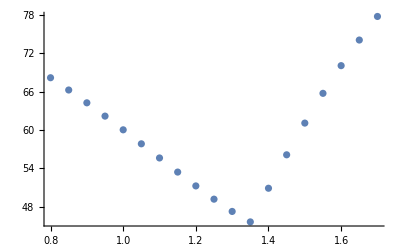

```mathematica
ListPlot[Table[{rp,SolGSCauchyFixedRMod1A[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkA2,10,λA,ΔsA1,ϵcA,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,RA,χsA,WxminHA,zH3O,xCL,kharA,RA,-1.0,rp]},{rp,0.8,1.7,0.05}]]
```

```mathematica
ϵcB=0;ΔkB=50;
```

G^R: 29.9398

ΔGkF: 31.7906

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

ΔGG: 31.7906

G^R: 16.5287

ΔGkF: 43.2808

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

ΔGG: 43.2808

G^R: 8.97573

ΔGkF: 48.8286

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

ΔGG: 48.8286

G^R: 5.74636

ΔGkF: 49.9771

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

ΔGG: 49.9771

G^R: 5.65624

ΔGkF: 47.923

ΔGG: 47.923

G^R: 7.79559

ΔGkF: 43.5929

ΔGG: 43.5929

G^R: 11.4696

ΔGkF: 37.704

ΔGG: 37.704

G^R: 16.1515

ΔGkF: 30.8129

ΔGG: 30.8129

G^R: 21.4449

ΔGkF: 23.3537

ΔGG: 23.3537

G^R: 27.0554

ΔGkF: 15.6694

ΔGG: 15.6694

G^R: 32.7669

ΔGkF: 8.03671

ΔGG: 8.03671

G^R: 38.4239

ΔGkF: 0.687362

ΔGG: 1.51993

G^R: 43.9171

ΔGkF: -6.17514

ΔGG: 0.80836

G^R: 49.1728

ΔGkF: -12.3605

ΔGG: 0.57663

G^R: 54.1438

ΔGkF: -17.6783

ΔGG: 0.438786

G^R: 58.803

ΔGkF: -21.9263

ΔGG: 0.349289

G^R: 63.138

ΔGkF: -24.8786

ΔGG: 0.294544

G^R: 67.1471

ΔGkF: -26.2737

ΔGG: 0.27042

G^R: 70.8364

ΔGkF: -25.8028

ΔGG: 0.278447

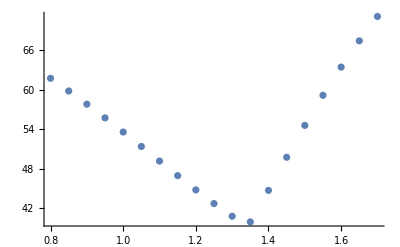

```mathematica
ListPlot[Table[{rp,SolGSCauchyFixedRMod1[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkB,0,λA,ΔsA1,ϵcB,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,RA,χsA,WxminHA,zH3O,xCL,kharA,RA,-1.0,rp]},{rp,0.8,1.7,0.05}]]
```

G^R: 29.9398

ΔGkF: 51.7906

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

ΔGG: 51.7906

G^R: 16.5287

ΔGkF: 63.2808

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

ΔGG: 63.2808

G^R: 8.97573

ΔGkF: 68.8286

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

ΔGG: 68.8286

G^R: 5.74636

ΔGkF: 69.9771

ΔGG: 69.9771

G^R: 5.65624

ΔGkF: 67.923

ΔGG: 67.923

G^R: 7.79559

ΔGkF: 63.5929

ΔGG: 63.5929

G^R: 11.4696

ΔGkF: 57.704

ΔGG: 57.704

G^R: 16.1515

ΔGkF: 50.8129

ΔGG: 50.8129

G^R: 21.4449

ΔGkF: 43.3537

ΔGG: 43.3537

G^R: 27.0554

ΔGkF: 35.6694

ΔGG: 35.6694

G^R: 32.7669

ΔGkF: 28.0367

ΔGG: 28.0367

G^R: 38.4239

ΔGkF: 20.6874

ΔGG: 20.6874

G^R: 43.9171

ΔGkF: 13.8249

ΔGG: 13.8249

G^R: 49.1728

ΔGkF: 7.63954

ΔGG: 7.63954

G^R: 54.1438

ΔGkF: 2.32171

ΔGG: 2.23128

G^R: 58.803

ΔGkF: -1.92633

ΔGG: 1.09753

G^R: 63.138

ΔGkF: -4.87857

ΔGG: 0.877087

G^R: 67.1471

ΔGkF: -6.27368

ΔGG: 0.803565

G^R: 70.8364

ΔGkF: -5.80275

ΔGG: 0.826984

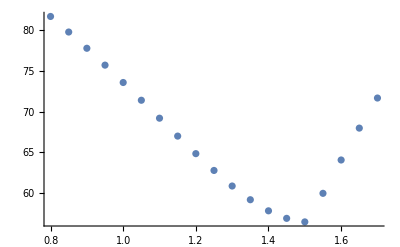

```mathematica
ListPlot[Table[{rp,SolGSCauchyFixedRMod1[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkB,20,λA,ΔsA1,ϵcB,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,RA,χsA,WxminHA,zH3O,xCL,kharA,RA,-1.0,rp]},{rp,0.8,1.7,0.05}]]
```

G^R: 49.9398

ΔGkF: 11.7906

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

ΔGG: 11.7906

G^R: 36.5287

ΔGkF: 23.2808

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

ΔGG: 23.2808

G^R: 28.9757

ΔGkF: 28.8286

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

ΔGG: 28.8286

G^R: 25.7464

ΔGkF: 29.9771

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

ΔGG: 29.9771

G^R: 25.6562

ΔGkF: 27.923

ΔGG: 27.923

G^R: 27.7956

ΔGkF: 23.5929

ΔGG: 23.5929

G^R: 31.4696

ΔGkF: 17.704

ΔGG: 17.704

G^R: 36.1515

ΔGkF: 10.8129

ΔGG: 10.8129

G^R: 41.4449

ΔGkF: 3.35375

ΔGG: 3.35107

G^R: 47.0554

ΔGkF: -4.33063

ΔGG: 0.909913

G^R: 52.7669

ΔGkF: -11.9633

ΔGG: 0.588557

G^R: 58.4239

ΔGkF: -19.3126

ΔGG: 0.402638

G^R: 63.9171

ΔGkF: -26.1751

ΔGG: 0.27209

G^R: 69.1728

ΔGkF: -32.3605

ΔGG: 0.176078

G^R: 74.1438

ΔGkF: -37.6783

ΔGG: 0.105783

G^R: 78.803

ΔGkF: -41.9263

ΔGG: 0.0564088

G^R: 83.138

ΔGkF: -44.8786

ΔGG: 0.0252447

G^R: 87.1471

ΔGkF: -46.2737

ΔGG: 0.0113532

G^R: 90.8364

ΔGkF: -45.8028

ΔGG: 0.0159842

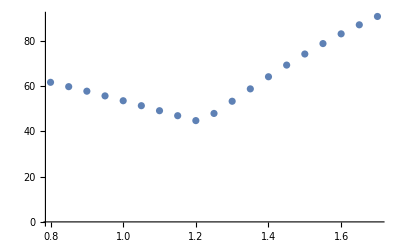

```mathematica
ListPlot[Table[{rp,SolGSCauchyFixedRMod1[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkB,-20,λA,ΔsA1,ϵcB,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,RA,χsA,WxminHA,zH3O,xCL,kharA,RA,-1.0,rp]},{rp,0.8,1.7,0.05}]]
```

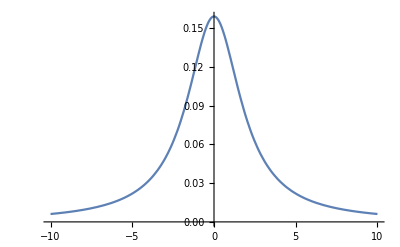

```mathematica
Plot[1/(2π(1+(x/2)^2)),{x,-10,10}]
```

```mathematica
Integrate[1/π(γ/2)/(γ^2/4+(ϵk-ϵc)^2)1/(ϵk-dG),{ϵk,-∞,0},Assumptions->{γ>0,ϵc∈Reals,dG∈Reals}]
```

ConditionalExpression[-(2 dG π-2 π ϵc+4 (-dG+ϵc) ArcTan[(2 ϵc)/γ]-γ Log[4]+γ Log[(γ^2+4 ϵc^2)/dG^2])/(π (γ^2+4 (dG-ϵc)^2)),dG≥0]

Diagonalization of Solution Phase FES along Proton Coordinate rp by Solving 1D Schrodinger Equation at each X (and R)

Input parameters:
   DE1 - dissociation energy (kcal/mol);
	DE2 - dissociation energy (kcal/mol);
	ω1 - vibrational frequency (cm-1);
	ω2- beta parameter (cm-1);
	W - coupling parameter between reactor and product diabatic states, in kcal/mol; 
	ΔkF - intrinsic bias, ϵ_D+J_DD-ϵ_kF+const., in kcal/mol;
	X - diabatic solvation energy gap, in kcal/mol; 
	λ - solvent reorganization energy, in kcal/mol; 
	Δs - difference in equilibrium solvation energy, in kcal/mol;
	ϵc - center of band relative to Fermi level, in kcal/mol; 
	γ - parameter equal to half FWHM in Cauchy-Lorentzian DOS distribution, in kcal/mol; 
	T -- temperature, in K; 
	x1A -- distance of contact layer plane (CLP) from electrode surface,in Å;
	x2A -- distance of outer Helmholtz plane (OHP) from CLP, in Å
	εI -- relative permittivity (dielectric constant) of contact layer (CL), assumed independent of η;
	ε -- relative permittivity of diffuse layer, assumed independent of E and equal to pure bulk solvent; 
	c0ions -- concentration of cations in solution containing only monovalent ions, in M;
	xA -- distance from electrode surface, in Å, usually set equal to R;
	R - distance between donor and acceptor, in Å; 
	E-- applied potential, in V vs. E_PZC; 
	δ - grid size , in Å;
	
Select local variables:
      rp - distance from minima of left PES, in Å;
	G1 - solution phase free energy of reactant state, in kcal/mol;
	ΔGelst -  reaction free energy contribution of electric field, in kcal/mol;
	ΔGkF - Volmer reaction free energy for reaction involving an electron at Fermi level, in kcal/mol;
	ΔGG - Volmer reaction free energy considering all filled bands, in kcal/mol;
	Gsol - GS adiabatic FES at each X and R as a function of rp, in kcal/mol;
	μ - reduced mass, in amu;
	KE - kinetic energy, in au.

Cauchy-Lorentzian distribution used to model DOS

```mathematica
CauchyFixedRXDiagGS[DE1_,ω1_,DE2_,ω2_,rDH_,rAH_,W_,ΔkF_,X_,λ_,Δs_,ϵc_,γ_,T_,x1A_,x2A_,εI_,ε_,c0ions_,xA_,χs_,R_,E_,offset_,δ_,nRoots_,OptionsPattern[{M->mH,DiffOrder->4}]]:=Module[{Ggrid,Gmin,Fgrid,nOrder,dims,ndim,Ranges,tuples,μ,KE,DiagMat,h,en,v,WvFn1,WvFn2,EigenVals},
Ggrid=ParallelTable[SolGSCauchyFixedR[DE1,ω1,DE2,ω2,rDH,rAH,W,ΔkF,X,λ,Δs,ϵc,γ,T,x1A,x2A,εI,ε,c0ions,xA,χs,R,E,rp,offset]*kcal2au,{rp,0.7,R-rAH+0.35,δ}];
Gmin=Min[Ggrid];Print["Gmin (kcal/mol) = ",Gmin*au2kcal];
Fgrid=Ggrid-Gmin;
nOrder=OptionValue[DiffOrder];
dims=Dimensions[Fgrid];
ndim=Length[dims];
Ranges=Table[Range[1,dims⟦idim⟧],{idim,1,ndim}];
tuples=Tuples[Ranges];
μ=OptionValue[M];
KE=-1/(2 μ (δ*a2bohr)^2) Sum[
NDSolve`FiniteDifferenceDerivative[i,Ranges,"DifferenceOrder"->nOrder]["DifferentiationMatrix"],
{i,DiagonalMatrix[Table[2,{i,1,ndim}]]}];
DiagMat=DiagonalMatrix[SparseArray[(Fgrid⟦##⟧&@@@tuples)]];
h=N[KE+DiagMat];
en=Reverse@Re@Eigenvalues[h,-nRoots,Method->{"Arnoldi","Criteria"->"RealPart"}];
v=Reverse@Re@Eigenvectors[h,-nRoots,Method->{"Arnoldi","Criteria"->"RealPart"}];
(*
WvFn1={en,Table[ArrayReshape[v⟦i⟧,dims],{i,1,Length[v]}]}⟦2,1⟧;(* Generate wavefunction with lowest eigenvalue *)
Print[WvFn1];
WvFn2={en,Table[ArrayReshape[v⟦i⟧,dims],{i,1,Length[v]}]}⟦2,2⟧;(* Generate wavefunction with second lowest eigenvalue *)
Print[WvFn2];
*)
EigenVals=({en,Table[ArrayReshape[v⟦i⟧,dims],{i,1,Length[v]}]}⟦1⟧+Gmin)au2kcal;
Print["10 lowest eigenvalues (kcal/mol) = ",EigenVals];
Min[EigenVals]
];
```

```mathematica
CauchyFixedRXDiagGSMod[DE1_,ω1_,DE2_,ω2_,rDH_,rAH_,W_,ΔkF_,X_,λ_,Δs_,ϵc_,γ_,T_,x1A_,x2A_,εI_,ε_,c0ions_,xA_,χs_,WxminHA_,zHA_,xmin_,khar_,R_,E_,offset_,δ_,nRoots_,OptionsPattern[{M->mH,DiffOrder->4}]]:=Module[{Ggrid,Gmin,Fgrid,nOrder,dims,ndim,Ranges,tuples,μ,KE,DiagMat,h,en,v,WvFn1,WvFn2,EigenVals},
Ggrid=ParallelTable[SolGSCauchyFixedRMod[DE1,ω1,DE2,ω2,rDH,rAH,W,ΔkF,X,λ,Δs,ϵc,γ,T,x1A,x2A,εI,ε,c0ions,xA,χs,WxminHA,zHA,xmin,khar,R,E,rp]*kcal2au,{rp,0.7,R-rAH+0.35,δ}];
Gmin=Min[Ggrid];Print["Gmin (kcal/mol) = ",Gmin*au2kcal];
Fgrid=Ggrid-Gmin;
nOrder=OptionValue[DiffOrder];
dims=Dimensions[Fgrid];
ndim=Length[dims];
Ranges=Table[Range[1,dims⟦idim⟧],{idim,1,ndim}];
tuples=Tuples[Ranges];
μ=OptionValue[M];
KE=-1/(2 μ (δ*a2bohr)^2) Sum[
NDSolve`FiniteDifferenceDerivative[i,Ranges,"DifferenceOrder"->nOrder]["DifferentiationMatrix"],
{i,DiagonalMatrix[Table[2,{i,1,ndim}]]}];
DiagMat=DiagonalMatrix[SparseArray[(Fgrid⟦##⟧&@@@tuples)]];
h=N[KE+DiagMat];
en=Reverse@Re@Eigenvalues[h,-nRoots,Method->{"Arnoldi","Criteria"->"RealPart"}];
v=Reverse@Re@Eigenvectors[h,-nRoots,Method->{"Arnoldi","Criteria"->"RealPart"}];
(*
WvFn1={en,Table[ArrayReshape[v⟦i⟧,dims],{i,1,Length[v]}]}⟦2,1⟧;(* Generate wavefunction with lowest eigenvalue *)
Print[WvFn1];
WvFn2={en,Table[ArrayReshape[v⟦i⟧,dims],{i,1,Length[v]}]}⟦2,2⟧;(* Generate wavefunction with second lowest eigenvalue *)
Print[WvFn2];
*)
EigenVals=({en,Table[ArrayReshape[v⟦i⟧,dims],{i,1,Length[v]}]}⟦1⟧+Gmin)au2kcal;
Print["10 lowest eigenvalues (kcal/mol) = ",EigenVals];
Min[EigenVals]
];
```

Cauchy-Lorentzian distribution used to model DOS; Hermite polynomial used to extrapolate

```mathematica
CauchyFixedRXDiagGSExt[DE1_,ω1_,DE2_,ω2_,rDH_,rAH_,W_,ΔkF_,X_,λ_,Δs_,ϵc_,γ_,T_,x1A_,x2A_,εI_,ε_,c0ions_,xA_,χs_,R_,E_,offset_,δ_,nRoots_,OptionsPattern[{M->mH,DiffOrder->4,IntOrder->2}]]:=Module[{Ggrid,Gmin,Spl,Fgrid,intorder,nOrder,dims,ndim,Ranges,tuples,μ,KE,DiagMat,h,en,v,WvFn1,WvFn2,EigenVals},
Ggrid=ParallelTable[{rp,SolGSCauchyFixedR[DE1,ω1,DE2,ω2,rDH,rAH,W,ΔkF,X,λ,Δs,ϵc,γ,T,x1A,x2A,εI,ε,c0ions,xA,χs,R,E,rp,offset]*kcal2au},{rp,0.85,R-rAH+0.2,δ}];
Gmin=Min[Ggrid];Print["Gmin (kcal/mol) = ",Gmin*au2kcal];
intorder=OptionValue[IntOrder];
Spl=Interpolation[Ggrid-Gmin,InterpolationOrder->intorder];
Fgrid=ParallelTable[Spl[rp],{rp,0.6,R-rAH+0.4,0.0005}];
nOrder=OptionValue[DiffOrder];
dims=Dimensions[Fgrid];
ndim=Length[dims];
Ranges=Table[Range[1,dims⟦idim⟧],{idim,1,ndim}];
tuples=Tuples[Ranges];
μ=OptionValue[M];
KE=-1/(2 μ (0.0005*a2bohr)^2) Sum[
NDSolve`FiniteDifferenceDerivative[i,Ranges,"DifferenceOrder"->nOrder]["DifferentiationMatrix"],
{i,DiagonalMatrix[Table[2,{i,1,ndim}]]}];
DiagMat=DiagonalMatrix[SparseArray[(Fgrid⟦##⟧&@@@tuples)]];
h=N[KE+DiagMat];
en=Reverse@Re@Eigenvalues[h,-nRoots,Method->{"Arnoldi","Criteria"->"RealPart"}];
v=Reverse@Re@Eigenvectors[h,-nRoots,Method->{"Arnoldi","Criteria"->"RealPart"}];
(*
WvFn1={en,Table[ArrayReshape[v⟦i⟧,dims],{i,1,Length[v]}]}⟦2,1⟧;(* Generate wavefunction with lowest eigenvalue *)
(* Print[WvFn1]; *)
WvFn2={en,Table[ArrayReshape[v⟦i⟧,dims],{i,1,Length[v]}]}⟦2,2⟧;(* Generate wavefunction with second lowest eigenvalue *)
Print[WvFn2];
*)
EigenVals=({en,Table[ArrayReshape[v⟦i⟧,dims],{i,1,Length[v]}]}⟦1⟧+Gmin)au2kcal;
(* Print["10 lowest eigenvalues (kcal/mol) = ",EigenVals]; *)
Min[EigenVals]
];
```

Construction of proton-quantized 1D-FES at each R as a function of X

Input parameters:
   DE1 - dissociation energy (kcal/mol);
	DE2 - dissociation energy (kcal/mol);
	ω1 - vibrational frequency (cm-1);
	ω2- beta parameter (cm-1);
	W - coupling parameter between reactor and product diabatic states, in kcal/mol; 
	ΔkF - intrinsic bias, ϵ_D+J_DD-ϵ_kF+const., in kcal/mol;
	λ - solvent reorganization energy, in kcal/mol; 
	Δs - difference in equilibrium solvation energy, in kcal/mol;
	ϵc - center of band relative to Fermi level, in kcal/mol; 
	γ - parameter equal to half FWHM in Cauchy-Lorentzian DOS distribution, in kcal/mol; 
	T -- temperature, in K; 
	x1A -- distance of contact layer plane (CLP) from electrode surface,in Å;
	x2A -- distance of outer Helmholtz plane (OHP) from CLP, in Å
	εI -- relative permittivity (dielectric constant) of contact layer (CL), assumed independent of η;
	ε -- relative permittivity of diffuse layer, assumed independent of η and equal to pure bulk solvent; 
	c0ions -- concentration of cations in solution containing only monovalent ions, in M;
	xA -- distance from electrode surface, in Å, usually set equal to R;
	R - distance between donor and acceptor, in Å; 
	E-- applied potential, in V vs. E_PZC; 
	δ - grid size , in Å;

Select local variables:
      X - diabatic solvation energy gap, in kcal/mol.

Cauchy-Lorentzian distribution used to model DOS

```mathematica
GS1DFESCauchyFixedR[DE1_,ω1_,DE2_,ω2_,rDH_,rAH_,W_,ΔkF_,λ_,Δs_,ϵc_,γ_,T_,x1A_,x2A_,εI_,ε_,c0ions_,xA_,χs_,R_,E_,offset_,δ_,nRoots_,OptionsPattern[{M->mH,DiffOrder->4}]]:=Module[{nOrder,μ},
μ=OptionValue[M];
nOrder=OptionValue[DiffOrder];
Table[{X,CauchyFixedRXDiagGS[DE1,ω1,DE2,ω2,rDH,rAH,W,ΔkF,X,λ,Δs,ϵc,γ,T,x1A,x2A,εI,ε,c0ions,xA,χs,R,E,offset,δ,nRoots,M->μ,DiffOrder->nOrder]},{X,-12,12,1}]
];
```

```mathematica
GS1DFESCauchyFixedRMod[DE1_,ω1_,DE2_,ω2_,rDH_,rAH_,W_,ΔkF_,λ_,Δs_,ϵc_,γ_,T_,x1A_,x2A_,εI_,ε_,c0ions_,xA_,χs_,WxminHA_,zHA_,xmin_,khar_,R_,E_,offset_,δ_,nRoots_,OptionsPattern[{M->mH,DiffOrder->4}]]:=Module[{nOrder,μ},
μ=OptionValue[M];
nOrder=OptionValue[DiffOrder];
Table[{X,CauchyFixedRXDiagGSMod[DE1,ω1,DE2,ω2,rDH,rAH,W,ΔkF,X,λ,Δs,ϵc,γ,T,x1A,x2A,εI,ε,c0ions,xA,χs,WxminHA,zHA,xmin,khar,R,E,offset,δ,nRoots,M->μ,DiffOrder->nOrder]},{X,-12,12,1}]
];
```

```mathematica
GS1DFESCauchyFixedRExt[DE1_,ω1_,DE2_,ω2_,rDH_,rAH_,W_,ΔkF_,λ_,Δs_,ϵc_,γ_,T_,x1A_,x2A_,εI_,ε_,c0ions_,xA_,χs_,R_,E_,offset_,δ_,nRoots_,OptionsPattern[{M->mH,DiffOrder->4,IntOrder->2}]]:=Module[{intorder,nOrder,μ},
μ=OptionValue[M];
intorder=OptionValue[IntOrder];
nOrder=OptionValue[DiffOrder];
Table[{X,CauchyFixedRXDiagGS[DE1,ω1,DE2,ω2,rDH,rAH,W,ΔkF,X,λ,Δs,ϵc,γ,T,x1A,x2A,εI,ε,c0ions,xA,χs,R,E,offset,δ,nRoots,M->μ,DiffOrder->nOrder]},{X,-12,12,1}]
];
```

Construction of proton-quantized 2D-FES as a function of X and R

Input parameters:
   DE1 - dissociation energy (kcal/mol);
	DE2 - dissociation energy (kcal/mol);
	ω1 - vibrational frequency (cm-1);
	ω2- beta parameter (cm-1);
	W - coupling parameter between reactor and product diabatic states, in kcal/mol; 
	ΔkF - intrinsic bias, ϵ_D+J_DD-ϵ_kF+const., in kcal/mol;
	λ - solvent reorganization energy, in kcal/mol; 
	Δs - difference in equilibrium solvation energy, in kcal/mol;
	ϵc - center of band relative to Fermi level, in kcal/mol; 
	γ - parameter equal to half FWHM in Cauchy-Lorentzian DOS distribution, in kcal/mol; 
	T -- temperature, in K; 
	x1A -- distance of contact layer plane (CLP) from electrode surface,in Å;
	x2A -- distance of outer Helmholtz plane (OHP) from CLP, in Å
	εI -- relative permittivity (dielectric constant) of contact layer (CL), assumed independent of η;
	ε -- relative permittivity of diffuse layer, assumed independent of η and equal to pure bulk solvent; 
	c0ions -- concentration of cations in solution containing only monovalent ions, in M;
	E-- applied potential, in V vs. E_PZC; 
	δ - grid size along rp , in Å;
            WxminHA -- non-electrostatic work term for moving HA from bulk solution to xmin (vide infra), in eV;
             WxminA -- non-electrostatic work term for moving A from bulk solution to xmin (vide infra), in eV;
             zHA -- charge of HA;
             xmin -- local concentration maxima of HA closest to electrode surface, in Å (equal to x1A for H2O and presumably, H3O+);

Select local variables:
      X - diabatic solvation energy gap, in kcal/mol; 
	R - distance between donor and acceptor, in Å; 
	WtotHA - total work for moving HA from bulk solution to xmin, in eV.

Cauchy-Lorentzian distribution used to model DOS

```mathematica
GS2DFESCauchy[DE1_,ω1_,DE2_,ω2_,rDH_,rAH_,W_,ΔkF_,λ_,Δs_,ϵc_,γ_,T_,x1A_,x2A_,εI_,ε_,c0ions_,χs_,E_,δ_,nRoots_,δR_,zHA_,WxminHA_,khar_,xmin_,OptionsPattern[{M->mH,DiffOrder->4}]]:=Module[{WtotHA,nOrder,μ},
μ=OptionValue[M];
nOrder=OptionValue[DiffOrder];
Table[{X,R,CauchyFixedRXDiagGS[DE1,ω1,DE2,ω2,rDH,rAH,W,ΔkF,X,λ,Δs,ϵc,γ,T,x1A,x2A,εI,ε,c0ions,R,χs,R,E,0,δ,nRoots,M->μ,DiffOrder->nOrder]+WHAx[T,E,x1A,x2A,εI,ε,c0ions,WxminHA,zHA,x1A,khar,R]*ev2kcal},{X,-12,12,1},{R,2.70,3.60,δR}]
];
```

```mathematica
GS2DFESCauchyMod[DE1_,ω1_,DE2_,ω2_,rDH_,rAH_,W_,ΔkF_,λ_,Δs_,ϵc_,γ_,T_,x1A_,x2A_,εI_,ε_,c0ions_,χs_,E_,δ_,nRoots_,δR_,zHA_,WxminHA_,khar_,xmin_,OptionsPattern[{M->mH,DiffOrder->4}]]:=Module[{WtotHA,nOrder,μ},
μ=OptionValue[M];
nOrder=OptionValue[DiffOrder];
Table[{X,R,CauchyFixedRXDiagGSMod[DE1,ω1,DE2,ω2,rDH,rAH,W,ΔkF,X,λ,Δs,ϵc,γ,T,x1A,x2A,εI,ε,c0ions,R,χs,zHA,WxminHA,khar,x1A,R,E,0,δ,nRoots,M->μ,DiffOrder->nOrder]},{X,-12,12,1},{R,2.70,3.60,δR}]
];
```

Calculations

```mathematica
DE1A=100;ω1A=3500;DE2A=52.14;ω2A=1880;rDH=0.976;rAH=1.60;WA=10;λA=10.0;
ΔGelstA=-20;ΔsA1=20;ΔkA1=-30;ϵcA=-230 (* -10 eV *); γA=100;TT=298;xCL=3.2;xOHL=3.5;εCL=2;
c0ionsA=0.10;xAA=RA;RA=3.10;χsA=0;offset=0;
```

```mathematica
δRA=0.1;
zH3O=1;
WxminHA=0.3;
kharA=15;
```

```mathematica
BetaMorse[1880,DE2A,mH]
```

0.919473887

```mathematica
BetaMorse[3500,DE1A,mH]
```

1.21041584

```mathematica
MorseEnergy[0,1.21,100,{M->MassH}]
```

4.93925

```mathematica
MorseEnergy[1,1.21,100,{M->MassH}]
```

14.4425

```mathematica
MorseEnergy[0,0.9195,52.14,{M->MassH}]
```

2.70848

## Test Calculations

```mathematica
SolGSCauchyFixedR[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkA1,12,λA,ΔsA1,ϵcA,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,xAA,χsA,RA,-1.0,1.0,offset]
```

-99.9983

```mathematica
Table[{rp,SolGSCauchyFixedR[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkA1,10,λA,ΔsA1,ϵcA,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,xAA,χsA,RA,-1.0,rp,offset]},{rp,0.6,2.0,0.05}]
```

FindRoot::nlnum: The function value {Undefined} is not a list of numbers with dimensions {1} at {ΔGG$21866} = {-144.867}.

FindRoot::nlnum: The function value {Undefined} is not a list of numbers with dimensions {1} at {ΔGG$23390} = {-83.3045}.

FindRoot::nlnum: The function value {Undefined} is not a list of numbers with dimensions {1} at {ΔGG$24912} = {-39.6638}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

{{0.6,-59.0168},{0.65,-60.567},{0.7,-62.2111},{0.75,-63.9494},{0.8,-75.8908},{0.85,-89.2473},{0.9,-96.7821},{0.95,-100.008},{1.,-100.104},{1.05,-97.9793},{1.1,-94.3288},{1.15,-89.6858},{1.2,-84.4895},{1.25,-84.7862},{1.3,-86.7073},{1.35,-88.3997},{1.4,-89.769},{1.45,-90.6986},{1.5,-91.0455},{1.55,-90.6343},{1.6,-89.2516},{1.65,-86.6376},{1.7,-82.4773},{1.75,-76.3898},{1.8,-67.9148},{1.85,-56.4979},{1.9,-41.4716},{1.95,-22.0342},{2.,-18.7038}}

```mathematica
Min[{{0.6,-59.01682191577797},{0.65,-60.566989687541664},{0.7,-62.21108935975732},{0.75,-63.94935210631081},{0.8,-75.89075002186418},{0.85,-89.24728363894891},{0.9,-96.78205052128101},{0.95,-100.00802004464862},{1.,-100.10430738846492},{1.05,-97.97928621587971},{1.1,-94.32883852272111},{1.15,-89.6858010716334},{1.2000000000000002,-84.48946398762413},{1.25,-84.7861577254618},{1.3,-86.7073299901651},{1.35,-88.39974581410758},{1.4,-89.76901680517149},{1.4500000000000002,-90.69863308184011},{1.5,-91.04545035212762},{1.55,-90.63430352940046},{1.6,-89.25158163968513},{1.65,-86.63756783755389},{1.7000000000000002,-82.47731164624405},{1.75,-76.38975700091119},{1.8000000000000003,-67.91479803152549},{1.85,-56.49787326773731},{1.9,-41.471636296288395},{1.9500000000000002,-22.03415473497958},{2.,-18.703792319896696}}]
```

-100.104

```mathematica
Export["X10kcal.tsv",{{0.6,-59.01682191577797},{0.65,-60.566989687541664},{0.7,-62.21108935975732},{0.75,-63.94935210631081},{0.8,-75.89075002186418},{0.85,-89.24728363894891},{0.9,-96.78205052128101},{0.95,-100.00802004464862},{1.,-100.10430738846492},{1.05,-97.97928621587971},{1.1,-94.32883852272111},{1.15,-89.6858010716334},{1.2000000000000002,-84.48946398762413},{1.25,-84.7861577254618},{1.3,-86.7073299901651},{1.35,-88.39974581410758},{1.4,-89.76901680517149},{1.4500000000000002,-90.69863308184011},{1.5,-91.04545035212762},{1.55,-90.63430352940046},{1.6,-89.25158163968513},{1.65,-86.63756783755389},{1.7000000000000002,-82.47731164624405},{1.75,-76.38975700091119},{1.8000000000000003,-67.91479803152549},{1.85,-56.49787326773731},{1.9,-41.471636296288395},{1.9500000000000002,-22.03415473497958},{2.,-18.703792319896696}}]
```

X10kcal.tsv

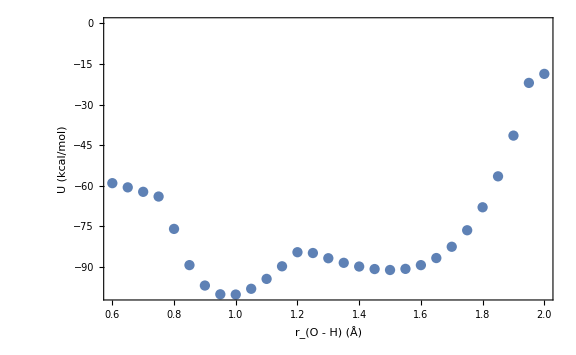

```mathematica
ListPlot[{{0.6,-59.01682191577797},{0.65,-60.566989687541664},{0.7,-62.21108935975732},{0.75,-63.94935210631081},{0.8,-75.89075002186418},{0.85,-89.24728363894891},{0.9,-96.78205052128101},{0.95,-100.00802004464862},{1.,-100.10430738846492},{1.05,-97.97928621587971},{1.1,-94.32883852272111},{1.15,-89.6858010716334},{1.2000000000000002,-84.48946398762413},{1.25,-84.7861577254618},{1.3,-86.7073299901651},{1.35,-88.39974581410758},{1.4,-89.76901680517149},{1.4500000000000002,-90.69863308184011},{1.5,-91.04545035212762},{1.55,-90.63430352940046},{1.6,-89.25158163968513},{1.65,-86.63756783755389},{1.7000000000000002,-82.47731164624405},{1.75,-76.38975700091119},{1.8000000000000003,-67.91479803152549},{1.85,-56.49787326773731},{1.9,-41.471636296288395},{1.9500000000000002,-22.03415473497958},{2.,-18.703792319896696}},Frame->True,FrameLabel->{"r_(O - H) (Å)","U (kcal/mol)"},FrameStyle->Black,LabelStyle->Large,ImageSize->Large]
```

```mathematica
Int1=Interpolation[{{0.8,-75.89075002186418},{0.85,-89.24728363894891},{0.9,-96.78205052128101},{0.95,-100.00802004464862},{1.,-100.10430738846492},{1.05,-97.97928621587971},{1.1,-94.32883852272111},{1.15,-89.6858010716334},{1.2000000000000002,-84.48946398762413},{1.25,-84.7861577254618},{1.3,-86.7073299901651},{1.35,-88.39974581410758},{1.4,-89.76901680517149},{1.4500000000000002,-90.69863308184011},{1.5,-91.04545035212762},{1.55,-90.63430352940046},{1.6,-89.25158163968513},{1.65,-86.63756783755389},{1.7000000000000002,-82.47731164624405},{1.75,-76.38975700091119},{1.8000000000000003,-67.91479803152549},{1.85,-56.49787326773731},{1.9,-41.471636296288395}},InterpolationOrder->2,Method->"Hermite"]
```

InterpolatingFunction[{{0.8, 1.9}}, <>]

InterpolatingFunction::dmval: Input value {0.500031} lies outside the range of data in the interpolating function. Extrapolation will be used.

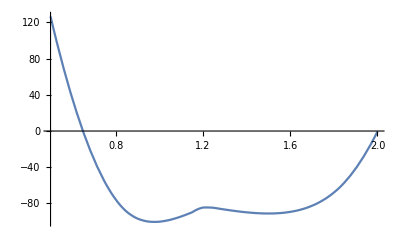

```mathematica
Plot[Int1[rp],{rp,0.5,2.0},PlotRange->All]
```

```mathematica
Table[{rp,SolGSCauchyFixedR[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkA1,-10,λA,ΔsA1,ϵcA,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,xAA,χsA,RA,-1.0,rp,offset]},{rp,0.6,2.0,0.05}]
```

FindRoot::nlnum: The function value {Undefined} is not a list of numbers with dimensions {1} at {ΔGG$64733} = {-164.867}.

FindRoot::nlnum: The function value {Undefined} is not a list of numbers with dimensions {1} at {ΔGG$66259} = {-103.305}.

FindRoot::nlnum: The function value {Undefined} is not a list of numbers with dimensions {1} at {ΔGG$67781} = {-59.6638}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

{{0.6,-69.0168},{0.65,-70.567},{0.7,-72.2111},{0.75,-73.9494},{0.8,-75.7805},{0.85,-79.4079},{0.9,-86.8772},{0.95,-90.0971},{1.,-90.2051},{1.05,-88.1321},{1.1,-88.3373},{1.15,-90.5465},{1.2,-92.7123},{1.25,-94.7862},{1.3,-96.7073},{1.35,-98.3997},{1.4,-99.769},{1.45,-100.699},{1.5,-101.045},{1.55,-100.634},{1.6,-99.2516},{1.65,-96.6376},{1.7,-92.4773},{1.75,-86.3898},{1.8,-77.9148},{1.85,-66.4979},{1.9,-51.4716},{1.95,-32.0342},{2.,-8.86625}}

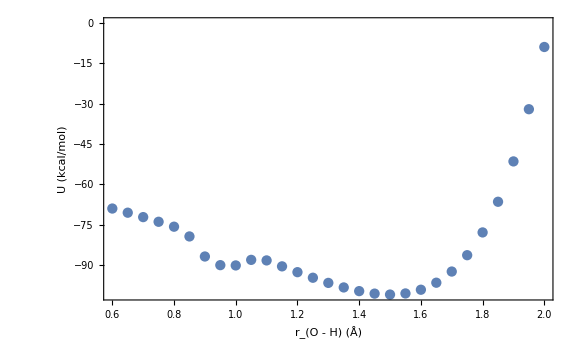

```mathematica
ListPlot[{{0.6,-69.01682191577797},{0.65,-70.56698968754166},{0.7,-72.21108935975732},{0.75,-73.94935210631081},{0.8,-75.7805253464002},{0.85,-79.40791813577388},{0.9,-86.87721559645058},{0.95,-90.09713129371579},{1.,-90.20510207292219},{1.05,-88.13205148588096},{1.1,-88.3372939441723},{1.15,-90.54654464686818},{1.2000000000000002,-92.71227454891181},{1.25,-94.7861577254618},{1.3,-96.7073299901651},{1.35,-98.39974581410758},{1.4,-99.76901680517149},{1.4500000000000002,-100.69863308184011},{1.5,-101.04545035212762},{1.55,-100.63430352940046},{1.6,-99.25158163968511},{1.65,-96.63756783755389},{1.7000000000000002,-92.47731164624405},{1.75,-86.38975700091117},{1.8000000000000003,-77.91479803152549},{1.85,-66.4978732677373},{1.9,-51.471636296288395},{1.9500000000000002,-32.03415473497958},{2.,-8.86625244302625}},Frame->True,FrameLabel->{"r_(O - H) (Å)","U (kcal/mol)"},FrameStyle->Black,LabelStyle->Large,ImageSize->Large]
```

```mathematica
Table[{rp,SolGSCauchyFixedR[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkA1,2,λA,ΔsA1,ϵcA,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,xAA,χsA,RA,-1.0,rp,offset]},{rp,0.6,2.0,0.05}]
```

FindRoot::nlnum: The function value {Undefined} is not a list of numbers with dimensions {1} at {ΔGG$150975} = {-152.867}.

FindRoot::nlnum: The function value {Undefined} is not a list of numbers with dimensions {1} at {ΔGG$152503} = {-91.3045}.

FindRoot::nlnum: The function value {Undefined} is not a list of numbers with dimensions {1} at {ΔGG$154027} = {-47.6638}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

{{0.6,-65.4168},{0.65,-66.967},{0.7,-68.6111},{0.75,-70.3494},{0.8,-74.3828},{0.85,-87.6815},{0.9,-95.2095},{0.95,-98.4344},{1.,-98.5327},{1.05,-96.413},{1.1,-92.776},{1.15,-88.2018},{1.2,-89.1123},{1.25,-91.1862},{1.3,-93.1073},{1.35,-94.7997},{1.4,-96.169},{1.45,-97.0986},{1.5,-97.4455},{1.55,-97.0343},{1.6,-95.6516},{1.65,-93.0376},{1.7,-88.8773},{1.75,-82.7898},{1.8,-74.3148},{1.85,-62.8979},{1.9,-47.8716},{1.95,-28.4342},{2.,-17.1381}}

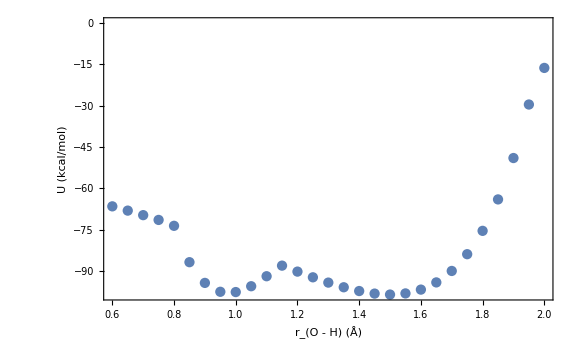

```mathematica
ListPlot[{{0.6,-66.51682191577797},{0.65,-68.06698968754166},{0.7,-69.71108935975732},{0.75,-71.44935210631081},{0.8,-73.5873307390529},{0.85,-86.79257579811026},{0.9,-94.31776508511942},{0.95,-97.54230367311571},{1.,-97.6412533822042},{1.05,-95.52387540109716},{1.1,-91.89387635450645},{1.15,-88.04654518448443},{1.2000000000000002,-90.21227454891181},{1.25,-92.2861577254618},{1.3,-94.2073299901651},{1.35,-95.89974581410758},{1.4,-97.26901680517149},{1.4500000000000002,-98.19863308184011},{1.5,-98.54545035212762},{1.55,-98.13430352940046},{1.6,-96.75158163968513},{1.65,-94.13756783755389},{1.7000000000000002,-89.97731164624405},{1.75,-83.88975700091119},{1.8000000000000003,-75.41479803152549},{1.85,-63.99787326773731},{1.9,-48.971636296288395},{1.9500000000000002,-29.53415473497958},{2.,-16.249234850859473}},Frame->True,FrameLabel->{"r_(O - H) (Å)","U (kcal/mol)"},FrameStyle->Black,LabelStyle->Large,ImageSize->Large]
```

```mathematica
CauchyFixedRXDiagGSExt[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkA1,12,λA,ΔsA1,ϵcA,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,xAA,χsA,RA,-1.0,offset,0.05,10,M->mH,DiffOrder->4,IntOrder->2]//Timing
```

Gmin (kcal/mol) = -99.9983

{3.9454,-95.3328}

```mathematica
CauchyFixedRXDiagGSExt[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkA1,12,λA,ΔsA1,ϵcA,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,xAA,χsA,RA,-1.0,offset,0.02,10,M->mH,DiffOrder->4,IntOrder->2]//Timing
```

10 lowest eigenvalues (kcal/mol) = {-95.3588,-86.6177,-85.7654,-80.8972,-76.5362,-72.7684,-72.7684,-68.0395,-60.7668,-53.2619}

{3.52246,-95.3588}

```mathematica
CauchyFixedRXDiagGS[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkA1,12,λA,ΔsA1,ϵcA,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,xAA,χsA,RA,-1.0,offset,0.01,10,M->mH,DiffOrder->4]//Timing
```

Gmin (kcal/mol) = -100.272

{-0.00195717,-0.000301551,0.00133174,0.00306159,0.00501143,0.00731774,0.0101389,0.013662,0.0180693,0.0234933,0.03005,0.0378335,0.0469067,0.0572914,0.0689602,0.0818298,0.0957574,0.11054,0.125918,0.141582,0.157185,0.172354,0.186706,0.199868,0.211492,0.221271,0.228953,0.234352,0.237356,0.237927,0.236104,0.231996,0.225774,0.21766,0.207918,0.196837,0.184721,0.171876,0.158595,0.145156,0.131809,0.118772,0.106228,0.0943249,0.0831749,0.0728559,0.0634152,0.0548731,0.0472268,0.0404552,0.0345228,0.0293841,0.024987,0.0212737,0.0181587,0.0155412,0.0133365,0.0114748,0.00989879,0.00856127,0.00742323,0.0064524,0.00562205,0.00490995,0.00429765,0.00376974,0.00331335,0.00291771,0.00257381,0.00227405,0.00201206,0.00178247,0.00158073,0.001403,0.00124604,0.00110709,0.000983801,0.000874181,0.000776528,0.000689391,0.000611526,0.000541866,0.000479493,0.000423616,0.000373548,0.000328693,0.000288529,0.000252598,0.000220495,0.00019186,0.000166371,0.000143737,0.000123694,0.000106001,0.0000904375,0.0000768001,0.0000649002,0.0000545632,0.0000456272,0.0000379419,0.000031368,0.0000257769,0.00002105,0.0000170788,0.0000137641,0.000011016,8.7537×10^-6,6.90464×10^-6,5.40456×10^-6,4.19684×10^-6,3.23201×10^-6,2.46722×10^-6,1.86567×10^-6,1.39599×10^-6,1.03168×10^-6,7.50493×10^-7}

{0.000808616,-0.00114878,-0.003169,-0.00536067,-0.00783856,-0.0107292,-0.0141766,-0.0183439,-0.0233607,-0.0292625,-0.0360378,-0.0436234,-0.0518967,-0.0606711,-0.0696955,-0.0786597,-0.0872041,-0.0949353,-0.101446,-0.106337,-0.109242,-0.109856,-0.107947,-0.103383,-0.0961404,-0.0863078,-0.074085,-0.0597737,-0.0437619,-0.0265036,-0.00849458,0.00975298,0.0277358,0.0449829,0.061076,0.0756649,0.0884791,0.0993327,0.108126,0.114841,0.119536,0.122333,0.123407,0.122974,0.121278,0.11858,0.115146,0.11124,0.107118,0.103021,0.0991786,0.0958025,0.0930916,0.0912238,0.0902477,0.0900869,0.0906641,0.0919085,0.0937537,0.0961363,0.0989941,0.102265,0.105885,0.10979,0.113913,0.118183,0.122527,0.126872,0.131141,0.135255,0.139136,0.142708,0.145895,0.148627,0.150836,0.152462,0.153453,0.153767,0.15337,0.152243,0.150376,0.147775,0.144457,0.140451,0.135801,0.130561,0.124794,0.118575,0.111983,0.105102,0.0980204,0.0908266,0.0836074,0.0764461,0.0694206,0.062602,0.056053,0.0498268,0.0439669,0.0385062,0.0334674,0.0288633,0.0246975,0.0209649,0.0176533,0.0147442,0.0122143,0.0100364,0.00818127,0.00661811,0.00531611,0.00424521,0.00337693,0.00268511,0.00214646,0.00174119}

10 lowest eigenvalues (kcal/mol) = {-95.356,-86.6038,-85.7497,-81.0222,-77.0415,-72.769,-67.5436,-62.1432,-59.3748,-56.0616}

{0.12798,-95.356}

```mathematica
CauchyFixedRXDiagGS[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkA1,12,λA,ΔsA1,ϵcA,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,xAA,χsA,RA,-1.0,offset,0.02,10,M->mH,DiffOrder->4]//Timing
```

Gmin (kcal/mol) = -100.26

{0.0128903,-0.00468519,-0.0233499,-0.0463967,-0.075658,-0.111583,-0.153154,-0.197908,-0.242224,-0.281892,-0.312858,-0.331967,-0.337512,-0.329476,-0.309408,-0.280032,-0.244691,-0.20678,-0.16929,-0.134517,-0.103952,-0.078333,-0.0577804,-0.0419901,-0.0304082,-0.0222273,-0.0164192,-0.0122562,-0.00924176,-0.00703618,-0.00540511,-0.00418578,-0.00326422,-0.00256006,-0.00201622,-0.00159189,-0.0012577,-0.000992397,-0.000780457,-0.000610463,-0.000473913,-0.000364377,-0.000276892,-0.000207533,-0.000153113,-0.000110979,-0.0000788765,-0.0000548695,-0.0000372912,-0.0000247178,-0.0000159513,-0.0000100058,-6.09133×10^-6,-3.59488×10^-6,-2.05681×10^-6,-1.14567×10^-6}

{-0.00284781,0.0123119,0.0296341,0.0503707,0.0741636,0.0990713,0.121788,0.138214,0.144353,0.13732,0.116161,0.0822359,0.03902,-0.00860029,-0.0553243,-0.0964415,-0.128594,-0.150152,-0.161192,-0.163167,-0.158426,-0.149715,-0.139788,-0.131183,-0.126119,-0.12585,-0.129668,-0.136847,-0.146696,-0.158512,-0.171538,-0.184953,-0.197873,-0.209385,-0.218592,-0.22468,-0.226983,-0.225054,-0.218716,-0.208095,-0.193621,-0.175991,-0.156108,-0.134996,-0.113694,-0.0931618,-0.0741971,-0.0573802,-0.0430494,-0.0313099,-0.0220683,-0.0150858,-0.010038,-0.00657388,-0.00436792,-0.00316539}

10 lowest eigenvalues (kcal/mol) = {-95.3221,-86.5739,-85.6796,-80.9879,-76.8867,-72.4944,-66.6865,-59.1061,-57.746,-57.746}

{2.23066,-95.3221}

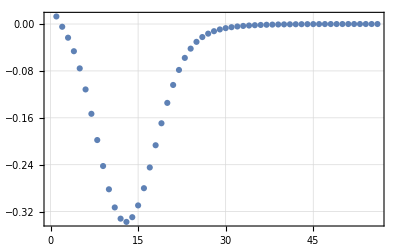

```mathematica
ListPlot[{0.012890262681972147,-0.004685190417461997,-0.023349916075771568,-0.04639671666110525,-0.0756579650611654,-0.11158314568314394,-0.15315413911126613,-0.1979081068762224,-0.24222428409429078,-0.28189245901046844,-0.31285849002649707,-0.33196670296262737,-0.3375122593368409,-0.3294755453240409,-0.3094076039885182,-0.28003188726258504,-0.24469069588433456,-0.20678012658875297,-0.16929033451455106,-0.13451660176634894,-0.10395226003958422,-0.0783329770114595,-0.05778041191641534,-0.04199005744098604,-0.03040824278231684,-0.022227256473563398,-0.016419151731034497,-0.012256152274795764,-0.00924176216671315,-0.00703617695734875,-0.005405111475981874,-0.004185781673090748,-0.00326422267590291,-0.0025600617662144983,-0.002016219244718184,-0.0015918871087192827,-0.0012577019873131086,-0.0009923968632002255,-0.0007804568917373473,-0.0006104631690853582,-0.00047391325061287454,-0.0003643768776184413,-0.00027689151272155117,-0.00020753259615017482,-0.0001531130479214631,-0.00011097899662377668,-0.00007887654693550316,-0.00005486945317563786,-0.00003729117121413617,-0.000024717795875938372,-0.00001595133641721942,-0.00001000577997753999,-6.091334067184451*^-6,-3.5948843854235403*^-6,-2.0568061769448554*^-6,-1.1456676009965649*^-6},PlotRange->All,PlotTheme->"Detailed"]
```

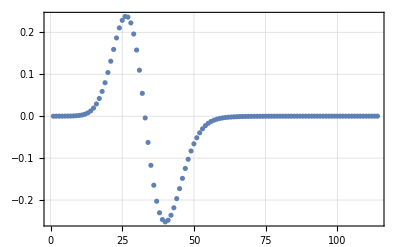

```mathematica
ListPlot[{-0.00009336537806662939,-0.00003784063317114493,6.741273161607884*^-6,0.000053225433450831284,0.00011472342238808935,0.0002082479668623149,0.0003592652347122103,0.0006083355234063621,0.0010214914981873896,0.001706857965762846,0.002841336943026835,0.004711928796698541,0.007758589069852502,0.012455080310486906,0.0193585924886418,0.029067672874907847,0.0421406528005192,0.058981237194342624,0.07970122315785061,0.10398002230482589,0.13094917033801748,0.1591339021426561,0.1864806122265216,0.21048760866556776,0.2284382194109376,0.2377135194700956,0.23614179038641325,0.22232862157226796,0.19590932600480127,0.15767549324745608,0.10954832990673352,0.05439847943216511,-0.004260749043363572,-0.06265833414511918,-0.11716890387572092,-0.16467523356203861,-0.20284191297821158,-0.23027098275965255,-0.24653201916565182,-0.2520791953584882,-0.24808276184813327,-0.23621030025407425,-0.21839388106506744,-0.1966141793850545,-0.17272379493856013,-0.1483218189547255,-0.12468211857644594,-0.10273026884335008,-0.08305922276966289,-0.0659716884626955,-0.05153732931145444,-0.0396546255381969,-0.030109790873919344,-0.02262784316725152,-0.01691286971388648,-0.012670602263160592,-0.009550087649506819,-0.007244716715801317,-0.005531823503409748,-0.004251654926092678,-0.0032892177551776774,-0.0025613351861681318,-0.002007540895171886,-0.0015836556776137468,-0.0012572367242003727,-0.0010043390188372056,-0.0008072000506136892,-0.0006525770647383513,-0.0005305474925882393,-0.00043363958124292455,-0.0003561994435467019,-0.0002939281159802137,-0.0002435413938563297,-0.00020251871403438395,-0.00016891689641904532,-0.00014123132630240994,-0.00011829198462562013,-0.00009918518617407147,-0.00008319436718570291,-0.00006975505458485688,-0.000058420446470129056,-0.00004883497690019581,-0.000040713926121252225,-0.00003382764036074608,-0.000027989293368417123,-0.000023045391145152313,-0.00001886841797844579,-0.00001535116522602192,-0.00001240238851022506,-9.943514795665456*^-6,-7.906176298442858*^-6,-6.230389433384015*^-6,-4.863228625486419*^-6,-3.7578701468558205*^-6,-2.8729025234887693*^-6,-2.171818987616761*^-6,-1.6226247521561973*^-6,-1.1975078627314325*^-6,-8.72536989775083*^-7,-6.273625057038428*^-7,-4.449082344027428*^-7,-3.110500950454935*^-7,-2.1428434744178772*^-7,-1.4539231293453516*^-7,-9.711048779128817*^-8,-6.381522862639145*^-8,-4.123010196991136*^-8,-2.6162015190175024*^-8,-1.6269815847517437*^-8,-9.866504339053*^-9,-5.7537588762880785*^-9,-3.085140011965722*^-9,-1.251872651025578*^-9,2.181044356799343*^-10},PlotRange->All,PlotTheme->"Detailed"]
```

```mathematica
CauchyFixedRXDiagGS[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkA1,12,λA,ΔsA1,ϵcA,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,xAA,χsA,RA,-1.0,offset,0.01,10,M->mH,DiffOrder->4]//Timing
```

Gmin (kcal/mol) = -100.272

{0.034347,0.0226799,0.0125866,0.00331962,-0.00574754,-0.0150807,-0.0250197,-0.0358017,-0.0475745,-0.0604021,-0.0742686,-0.0890803,-0.10467,-0.120804,-0.13719,-0.153491,-0.16934,-0.184356,-0.198163,-0.21041,-0.220782,-0.229023,-0.234939,-0.238411,-0.239397,-0.237931,-0.234119,-0.228131,-0.220191,-0.210564,-0.199543,-0.187437,-0.174557,-0.161203,-0.14766,-0.134183,-0.120997,-0.108293,-0.0962217,-0.0849015,-0.0744142,-0.0648106,-0.0561135,-0.0483224,-0.0414175,-0.0353643,-0.0301178,-0.0256258,-0.0218306,-0.0186454,-0.0159676,-0.013711,-0.0118045,-0.0101899,-0.00881889,-0.00765176,-0.00665559,-0.00580311,-0.00507166,-0.00444236,-0.00389949,-0.0034299,-0.00302258,-0.00266829,-0.0023593,-0.00208906,-0.00185208,-0.0016437,-0.00145999,-0.00129764,-0.00115379,-0.00102607,-0.000912411,-0.000811081,-0.000720588,-0.000639656,-0.000567191,-0.000502251,-0.000444024,-0.000391805,-0.000344983,-0.000303023,-0.000265453,-0.000231859,-0.000201869,-0.000175152,-0.000151409,-0.000130368,-0.000111781,-0.0000954189,-0.0000810716,-0.0000685438,-0.0000576543,-0.0000482346,-0.0000401283,-0.0000331903,-0.0000272861,-0.0000222918,-0.0000180936,-0.0000145877,-0.0000116798,-9.28465×10^-6,-7.32618×10^-6,-5.73667×10^-6,-4.45644×10^-6,-3.43332×10^-6,-2.62206×10^-6,-1.9838×10^-6,-1.48542×10^-6,-1.09888×10^-6,-8.0068×10^-7}

{-0.0269614,-0.0182506,-0.0104687,-0.00318031,0.00397752,0.0112451,0.0187574,0.0265572,0.0346049,0.042786,0.0509201,0.0587712,0.0660618,0.0724895,0.0777455,0.0815351,0.0835973,0.0837243,0.0817762,0.0776935,0.0715028,0.0633184,0.053337,0.0418282,0.0291202,0.0155821,0.00160513,-0.0124176,-0.0261094,-0.039127,-0.0511743,-0.062012,-0.0714646,-0.0794218,-0.0858382,-0.0907287,-0.0941618,-0.0962515,-0.0971483,-0.0970297,-0.0960914,-0.0945391,-0.092582,-0.0904279,-0.0882792,-0.0863318,-0.0847747,-0.0837908,-0.0835504,-0.0841109,-0.0854152,-0.0874031,-0.0900174,-0.0932031,-0.0969053,-0.101068,-0.105633,-0.11054,-0.115722,-0.121112,-0.126636,-0.132216,-0.137771,-0.143217,-0.148468,-0.153435,-0.158032,-0.162174,-0.165778,-0.168768,-0.171074,-0.172636,-0.173403,-0.173336,-0.172411,-0.170617,-0.167957,-0.16445,-0.16013,-0.155045,-0.149257,-0.14284,-0.135877,-0.128462,-0.120691,-0.112667,-0.104494,-0.0962707,-0.0880964,-0.0800621,-0.0722514,-0.0647382,-0.0575857,-0.0508456,-0.0445576,-0.0387495,-0.0334374,-0.0286267,-0.0243128,-0.0204825,-0.0171154,-0.0141852,-0.0116612,-0.00950995,-0.00769631,-0.00618493,-0.00494124,-0.00393247,-0.00312843,-0.00250227,-0.00203111}

10 lowest eigenvalues (kcal/mol) = {-95.2695,-86.5138,-85.4643,-80.8799,-76.4368,-71.9208,-66.0554,-59.2328,-53.4448,-53.4448}

{6.05708,-95.2695}

```mathematica
CauchyFixedRXDiagGS[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkA1,5,λA,ΔsA1,ϵcA,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,xAA,χsA,RA,-1.0,offset,0.02,10,M->mH,DiffOrder->4]//Timing
```

Gmin (kcal/mol) = -99.7568

{0.0962474,0.0497232,0.0140967,-0.0185981,-0.0535723,-0.0931232,-0.137267,-0.184143,-0.230475,-0.27223,-0.305405,-0.326811,-0.334659,-0.328828,-0.31078,-0.283182,-0.249365,-0.212761,-0.176441,-0.142822,-0.113561,-0.0895963,-0.0712505,-0.0576839,-0.0476313,-0.0401479,-0.0345533,-0.0303536,-0.0271838,-0.0247695,-0.0229,-0.0214101,-0.0201686,-0.019071,-0.0180347,-0.0169969,-0.0159136,-0.0147589,-0.0135238,-0.0122149,-0.0108523,-0.00946615,-0.00809253,-0.00676948,-0.00553262,-0.00441151,-0.00342716,-0.00259066,-0.00190326,-0.00135756,-0.000939587,-0.000631274,-0.000413011,-0.000265881,-0.0001735,-0.000123511}

{0.0135329,0.00718888,0.00229648,-0.00216346,-0.00684679,-0.011999,-0.0175432,-0.0231464,-0.0283001,-0.0324268,-0.0349996,-0.0356495,-0.0342351,-0.0308579,-0.0258242,-0.0195673,-0.0125508,-0.00517619,0.00229156,0.00977571,0.0174209,0.0256194,0.0350204,0.0461827,0.0593642,0.0747281,0.0923296,0.112086,0.133745,0.156864,0.180793,0.204689,0.227539,0.24822,0.26557,0.278491,0.286054,0.287597,0.282819,0.271826,0.25515,0.233705,0.208712,0.181575,0.153749,0.126595,0.101268,0.0786291,0.0592079,0.0432077,0.0305502,0.0209458,0.0139766,0.00917832,0.00611404,0.0044392}

10 lowest eigenvalues (kcal/mol) = {-94.7432,-92.7618,-87.8978,-84.8133,-80.6452,-74.9922,-68.291,-64.284,-64.284,-56.6763}

{2.03469,-94.7432}

```mathematica
CauchyFixedRXDiagGS[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkA1,0,λA,ΔsA1,ϵcA,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,xAA,χsA,RA,-1.0,offset,0.02,10,M->mH,DiffOrder->4]//Timing
```

Gmin (kcal/mol) = -98.5305

{0.000229077,0.000546123,0.000972936,0.00158583,0.00244994,0.00359081,0.005002,0.00663999,0.00842588,0.010256,0.01202,0.013622,0.0150003,0.0161421,0.0170904,0.0179452,0.0188612,0.0200474,0.0217749,0.0243969,0.0283784,0.0341966,0.0420099,0.0519698,0.064213,0.078827,0.0958128,0.115048,0.136251,0.158957,0.182505,0.206042,0.228552,0.24891,0.265958,0.278603,0.285921,0.287256,0.282312,0.271198,0.254447,0.23297,0.207984,0.180887,0.153124,0.12605,0.10081,0.0782575,0.0589172,0.0429883,0.0303903,0.0208331,0.0138994,0.00912638,0.00607869,0.00441315}

{-0.00234986,-0.014319,-0.0288279,-0.0481736,-0.0740324,-0.106557,-0.144678,-0.186082,-0.22743,-0.264848,-0.294597,-0.313741,-0.320665,-0.315292,-0.298999,-0.274271,-0.244205,-0.212018,-0.180638,-0.152454,-0.129201,-0.111349,-0.0974913,-0.0864319,-0.0772355,-0.0691627,-0.0616241,-0.0541542,-0.046401,-0.0381242,-0.0291997,-0.0196246,-0.0095177,0.000885933,0.0112517,0.0211729,0.030209,0.0379308,0.0439684,0.0480555,0.0500623,0.0500136,0.0480864,0.0445891,0.0399236,0.0345376,0.0288745,0.0233285,0.0182114,0.013735,0.01001,0.00705779,0.00483237,0.0032467,0.00219953,0.00160104}

10 lowest eigenvalues (kcal/mol) = {-95.9012,-93.192,-90.6765,-86.09,-82.2809,-77.254,-70.0768,-67.371,-67.371,-59.3552}

{1.89271,-95.9012}

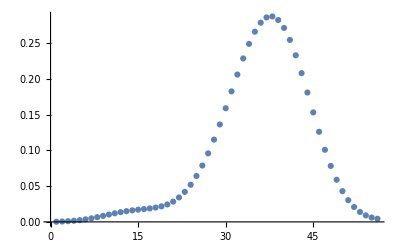

```mathematica
ListPlot[{0.00022907695008009477,0.0005461232564869245,0.0009729363282274654,0.001585833173320382,0.002449935783085435,0.00359080729558482,0.005002002300059223,0.006639994873968445,0.008425875903807892,0.010256014323767874,0.012020008410138065,0.013621959715891639,0.01500027750234818,0.016142080541065865,0.017090421208553735,0.017945218841335014,0.01886115618880014,0.02004740886497634,0.02177493505284206,0.02439691986116811,0.028378397656920067,0.03419663554285546,0.042009869641684454,0.051969813562427816,0.0642130220658209,0.07882699411356625,0.09581279335023052,0.1150476032357577,0.13625066238142114,0.15895714941707118,0.18250532363893204,0.2060422086755486,0.22855207904651648,0.2489098444594408,0.26595819607021615,0.2786034164938728,0.28592066676486155,0.287256163322862,0.2823118262073626,0.2711984525858709,0.2544466120412945,0.2329700801345404,0.2079839083301821,0.1808868280294368,0.15312400443486512,0.12604972832589187,0.10080954145129503,0.07825745645400492,0.058917193286039025,0.04298827289117588,0.030390258386127134,0.020833094811468007,0.013899440069220196,0.009126384457259494,0.006078687816679961,0.004413146912839402}]
```

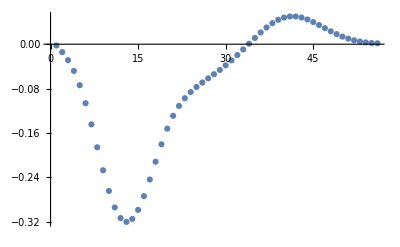

```mathematica
ListPlot[{-0.0023498624602378256,-0.014318992392821325,-0.028827932473792485,-0.048173581024421534,-0.07403239064561462,-0.10655684740219358,-0.1446779502484749,-0.1860822350461818,-0.22743011477567296,-0.2648483316931403,-0.29459652510129203,-0.3137411822068932,-0.32066487549414224,-0.31529193327981186,-0.29899948789822745,-0.27427066342515,-0.24420517834583613,-0.21201845496396995,-0.18063752194190583,-0.1524537483060277,-0.1292010201107426,-0.11134930251716318,-0.09749132746595635,-0.08643188542814186,-0.07723550848641264,-0.06916271981893066,-0.0616240603006645,-0.05415420765302974,-0.04640096895740575,-0.038124165218651106,-0.029199742188686997,-0.019624581130527178,-0.009517699129054563,0.000885933492396705,0.011251701188664174,0.02117294654159158,0.030209025375234906,0.03793077893539099,0.04396841343559721,0.04805546797810612,0.05006230316826416,0.050013573331564726,0.048086400600017995,0.044589086262622264,0.03992355327161853,0.03453757298841181,0.028874520467951737,0.023328520695374236,0.018211378859711917,0.013735022556856583,0.010010012087911519,0.00705778587209842,0.004832371673982642,0.0032467041307002215,0.0021995296115904714,0.0016010397594184754}]
```

```mathematica
CauchyFixedRXDiagGS[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkA1,-5,λA,ΔsA1,ϵcA,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,xAA,χsA,RA,-1.0,offset,0.02,10,M->mH,DiffOrder->4]//Timing
```

Gmin (kcal/mol) = -100.406

{0.0226546,0.0147342,0.0097915,0.00676502,0.0050099,0.00404728,0.00357189,0.00341485,0.00347998,0.00371013,0.0040715,0.00454753,0.005138,0.00586116,0.00675818,0.0079002,0.00939942,0.0114266,0.0142366,0.0181751,0.0234408,0.0302454,0.0388127,0.0493596,0.062071,0.0770696,0.0943819,0.113904,0.135367,0.158316,0.182095,0.205851,0.22857,0.249123,0.26635,0.279152,0.2866,0.288036,0.283159,0.272079,0.255326,0.233818,0.208775,0.1816,0.153748,0.126578,0.101242,0.0786008,0.0591808,0.043184,0.0305309,0.020931,0.0139657,0.00917045,0.0061084,0.0044349}

{-0.741749,-0.483485,-0.320343,-0.218187,-0.155889,-0.117467,-0.0926281,-0.0756166,-0.0631769,-0.053438,-0.0453324,-0.0382786,-0.0319917,-0.0263613,-0.0213681,-0.0170282,-0.0133583,-0.0103578,-0.00800373,-0.00624048,-0.00490345,-0.00386568,-0.00303537,-0.00234588,-0.00174846,-0.00120749,-0.000697379,-0.000200666,0.000293114,0.000788151,0.00128289,0.00177056,0.00223994,0.00267637,0.00306314,0.00338313,0.00362075,0.00376373,0.00380481,0.00374295,0.0035838,0.00333945,0.00302743,0.00266893,0.0022867,0.00190283,0.00153672,0.00120355,0.000913472,0.000671484,0.000477989,0.000329794,0.000221381,0.0001462,0.0000978748,0.0000712762}

10 lowest eigenvalues (kcal/mol) = {-97.7694,-97.1507,-92.7503,-89.7714,-86.8169,-81.7263,-76.076,-69.5223,-69.5223,-66.6912}

{2.19067,-97.7694}

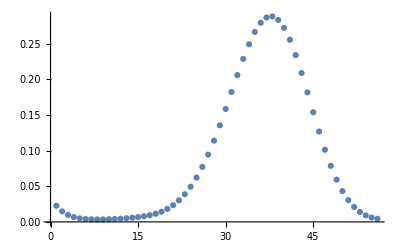

```mathematica
ListPlot[{0.022654613806649494,0.014734249286713167,0.009791502356029274,0.006765019078913136,0.00500990129148526,0.004047281157259691,0.0035718938565576274,0.003414850596738565,0.003479981379027092,0.0037101314574331107,0.004071498572308699,0.004547528983905064,0.005138000035390649,0.005861160828004644,0.006758176053213875,0.007900195358288706,0.009399421280369361,0.0114266047804106,0.01423657810347086,0.018175069990971557,0.023440820444964542,0.030245412044213237,0.03881269007354071,0.04935960577888106,0.06207102190641542,0.07706958014038501,0.09438191938068805,0.11390371010297234,0.1353672429886189,0.15831641767587978,0.18209464420105886,0.2058510984846073,0.228569706574225,0.24912303373821454,0.2663499914534884,0.27915227991825353,0.2866003625099071,0.2880363392841926,0.28315923332697146,0.2720786676210018,0.25532605874667197,0.23381809609229665,0.20877459197406464,0.1816004293360432,0.15374769106235123,0.1265776554844392,0.1012422604693144,0.07860079314412906,0.05918079450716868,0.0431840468435712,0.0305309195717657,0.020930976377191324,0.013965669760463217,0.009170454186388772,0.006108398942747726,0.004434899671037854}]
```

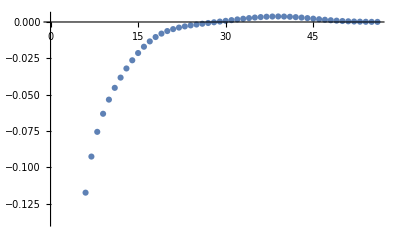

```mathematica
ListPlot[{-0.7417485408379912,-0.4834849623611839,-0.3203432312346962,-0.21818669695191611,-0.15588851729531508,-0.11746721792116986,-0.09262814731973328,-0.07561655943865025,-0.06317692670482912,-0.05343801121356512,-0.04533243660769705,-0.038278634732674024,-0.031991724628130394,-0.026361254946480884,-0.021368067078787002,-0.01702823808048577,-0.013358326152386033,-0.010357817131897026,-0.00800372507089358,-0.006240480419502564,-0.004903450002964502,-0.003865675822971754,-0.0030353660022925054,-0.0023458759806710403,-0.0017484621685943014,-0.001207492971714855,-0.0006973786566383121,-0.00020066552551864836,0.0002931140249830698,0.00078815132677106,0.0012828865076268425,0.001770557839183279,0.002239938593189867,0.0026763703931453066,0.0030631355409555623,0.0033831338825361748,0.00362075004980251,0.0037637266952122743,0.0038048132912853806,0.0037429516713932244,0.003583796898688677,0.0033394545345001537,0.0030274315039793605,0.002668926359312306,0.002286698957765357,0.0019028332637980004,0.0015367218659223018,0.0012035520733980499,0.0009134719424852589,0.0006714843087257805,0.0004779887077532824,0.00032979419336386513,0.0002213806655792104,0.00014619973436720215,0.00009787475570844422,0.00007127620730392652}]
```

```mathematica
CauchyFixedRXDiagGS[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkA1,-12,λA,ΔsA1,ϵcA,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,xAA,χsA,RA,-1.0,offset,0.02,10,M->mH,DiffOrder->4]//Timing
```

Gmin (kcal/mol) = -100.931

{-0.0000192006,5.31268×10^-6,0.0000308713,0.0000624279,0.000105729,0.000168206,0.000259685,0.000388976,0.000565945,0.000802591,0.00111443,0.00152282,0.00205874,0.00276855,0.00372281,0.00502924,0.00684437,0.00931279,0.0126009,0.0169037,0.0224412,0.0294511,0.0381767,0.0488486,0.0616617,0.076746,0.0941333,0.113723,0.13525,0.15826,0.182096,0.205909,0.228681,0.249284,0.266556,0.279396,0.286875,0.288332,0.283466,0.272387,0.255627,0.234102,0.209035,0.181832,0.153948,0.126745,0.101379,0.0787082,0.0592627,0.0432445,0.0305741,0.0209609,0.0139858,0.00918381,0.00611737,0.00444145}

{0.000109515,0.00032891,0.00059995,0.000961536,0.0014621,0.00216414,0.00314542,0.00444882,0.00610585,0.00814409,0.0105953,0.0135091,0.0169734,0.0211408,0.0262636,0.0327372,0.0411112,0.0516417,0.064501,0.0797889,0.0974885,0.117416,0.139169,0.162081,0.185194,0.207249,0.226717,0.241868,0.250886,0.252032,0.243835,0.225305,0.196129,0.156824,0.108821,0.054434,-0.00327791,-0.0607696,-0.114357,-0.16061,-0.196739,-0.220905,-0.232411,-0.231735,-0.220405,-0.200733,-0.17547,-0.147434,-0.119172,-0.0927255,-0.069495,-0.0502336,-0.0351319,-0.0239688,-0.0162913,-0.0116005}

10 lowest eigenvalues (kcal/mol) = {-98.293,-93.2025,-88.4904,-84.8174,-81.3618,-76.1699,-72.2149,-72.2149,-69.7074,-69.7074}

{2.97355,-98.293}

## Model Calculations

```mathematica
GS1DFESCauchy1Aa=GS1DFESCauchyFixedR[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkA1,λA,ΔsA1,ϵcA,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,xAA,χsA,RA,-1.0,offset,0.02,10,M->mH,DiffOrder->4]//Timing
```

Gmin (kcal/mol) = -100.945

{-0.0000115243,-1.54855×10^-6,8.08156×10^-6,0.0000194059,0.0000346907,0.0000568416,0.0000898796,0.000139534,0.000213884,0.000322253,0.000473598,0.000678606,0.000950756,0.00130811,0.00177627,0.00239308,0.00321575,0.00433163,0.00587168,0.00799209,0.0108459,0.0146137,0.0195036,0.0257455,0.0335817,0.0432516,0.0549715,0.0689075,0.0851449,0.103654,0.124254,0.14659,0.170106,0.194047,0.217474,0.239306,0.258388,0.273574,0.283838,0.28837,0.286682,0.278674,0.264668,0.245395,0.221938,0.195628,0.167912,0.140216,0.113812,0.0897146,0.0686223,0.0508981,0.036598,0.0255301,0.0173347,0.0115692,0.00779035,0.00562983}

10 lowest eigenvalues (kcal/mol) = {-98.2933,-93.2027,-88.4832,-84.7665,-81.1199,-75.524,-72.3704,-72.3704,-71.2644,-71.2644}

Gmin (kcal/mol) = -101.02

{-0.0000131447,-1.76192×10^-6,9.22751×10^-6,0.0000221514,0.0000395961,0.0000648777,0.000102585,0.000159247,0.000243953,0.000365521,0.000532775,0.000755925,0.00104752,0.0014242,0.00190958,0.00253876,0.00336508,0.00447039,0.00597983,0.00807377,0.0109082,0.0146619,0.0195413,0.0257755,0.0336058,0.0432713,0.0549876,0.0689208,0.0851558,0.103662,0.124261,0.146595,0.17011,0.194049,0.217475,0.239306,0.258386,0.273571,0.283834,0.288365,0.286677,0.278669,0.264662,0.245389,0.221933,0.195623,0.167907,0.140212,0.113808,0.089712,0.0686203,0.0508966,0.0365969,0.0255294,0.0173342,0.0115688,0.0077901,0.00562965}

10 lowest eigenvalues (kcal/mol) = {-98.3683,-93.2803,-88.6241,-85.2681,-81.5139,-75.8929,-72.4541,-72.4541,-71.3833,-71.3833}

Gmin (kcal/mol) = -101.045

{-0.0000152568,-2.03607×10^-6,0.0000107301,0.0000257457,0.0000460157,0.0000753932,0.000119209,0.00018503,0.000283146,0.000421766,0.000609566,0.000856203,0.00117318,0.00157562,0.0020851,0.0027341,0.00357251,0.00467726,0.00616662,0.00821662,0.0110173,0.0147462,0.0196075,0.0258281,0.0336482,0.0433058,0.0550159,0.068944,0.0851749,0.103678,0.124274,0.146605,0.170116,0.194053,0.217476,0.239305,0.258383,0.273566,0.283827,0.288357,0.286668,0.278659,0.264652,0.245379,0.221923,0.195614,0.1679,0.140205,0.113803,0.0897075,0.0686168,0.050894,0.0365949,0.025528,0.0173332,0.0115682,0.00778967,0.00562934}

10 lowest eigenvalues (kcal/mol) = {-98.3934,-93.3097,-88.7618,-85.8056,-81.8095,-76.2451,-72.4807,-72.4807,-71.4602,-71.4602}

Gmin (kcal/mol) = -101.02

{-0.0000179205,-2.34182×10^-6,0.0000127137,0.0000304345,0.0000543667,0.0000890586,0.000140797,0.000218411,0.000332548,0.000491484,0.000703604,0.000977735,0.001324,0.00175561,0.00229178,0.00296209,0.00381278,0.00491581,0.00638242,0.00838175,0.0111433,0.0148437,0.019684,0.0258889,0.0336972,0.0433456,0.0550486,0.0689709,0.0851969,0.103696,0.124288,0.146616,0.170124,0.194057,0.217478,0.239303,0.258379,0.27356,0.283819,0.288347,0.286657,0.278647,0.26464,0.245368,0.221912,0.195604,0.167891,0.140198,0.113796,0.0897023,0.0686127,0.0508909,0.0365927,0.0255264,0.0173321,0.0115674,0.00778916,0.00562897}

10 lowest eigenvalues (kcal/mol) = {-98.3685,-93.2902,-88.9067,-86.3131,-82.0237,-76.5869,-72.4364,-72.4364,-71.5206,-71.5206}

Gmin (kcal/mol) = -100.945

{-0.0000214525,-2.7383×10^-6,0.0000153637,0.0000366867,0.000065497,0.000107269,0.000169563,0.000262867,0.000398047,0.000583517,0.000827232,0.00113692,0.00152096,0.00199031,0.00256154,0.00326124,0.00413221,0.00524204,0.00669587,0.0086548,0.0113542,0.015007,0.019812,0.0259908,0.0337792,0.0434124,0.0551033,0.069016,0.0852339,0.103726,0.124312,0.146634,0.170137,0.194065,0.21748,0.239302,0.258373,0.27355,0.283805,0.288331,0.286639,0.278628,0.264621,0.245349,0.221894,0.195587,0.167876,0.140185,0.113786,0.0896937,0.068606,0.0508858,0.036589,0.0255237,0.0173303,0.0115662,0.00778833,0.00562836}

10 lowest eigenvalues (kcal/mol) = {-98.2937,-93.2243,-89.1193,-86.7444,-82.1685,-76.9185,-72.3142,-72.3142,-71.5672,-71.5672}

Gmin (kcal/mol) = -100.645

{0.0000321353,3.89993×10^-6,-0.0000234619,-0.000055743,-0.0000994007,-0.000162728,-0.000257153,-0.000398141,-0.00059616,-0.000859504,-0.00119423,-0.0016042,-0.00209226,-0.00266269,-0.00332488,-0.00409822,-0.00501815,-0.0061441,-0.00757036,-0.00944228,-0.0119796,-0.0154923,-0.0201928,-0.0262935,-0.0340229,-0.0436107,-0.0552659,-0.0691498,-0.0853436,-0.103815,-0.124382,-0.146687,-0.170174,-0.194087,-0.217488,-0.239296,-0.258354,-0.27352,-0.283765,-0.288283,-0.286585,-0.278571,-0.264562,-0.245291,-0.221839,-0.195537,-0.167831,-0.140146,-0.113754,-0.0896678,-0.0685858,-0.0508705,-0.0365778,-0.0255158,-0.0173248,-0.0115625,-0.00778582,-0.00562654}

10 lowest eigenvalues (kcal/mol) = {-97.9941,-92.9572,-89.8353,-87.1513,-82.3082,-77.4572,-71.8515,-71.8515,-71.6038,-71.6038}

Gmin (kcal/mol) = -100.145

{0.0000490134,3.32564×10^-6,-0.000041596,-0.000095243,-0.000168328,-0.000274693,-0.000433121,-0.000664002,-0.00097894,-0.00138474,-0.00188237,-0.00246716,-0.00313089,-0.00386565,-0.00466915,-0.00555079,-0.0065382,-0.00768461,-0.00907792,-0.0108537,-0.0132151,-0.0164592,-0.0209519,-0.026897,-0.0345087,-0.0440059,-0.0555898,-0.0694159,-0.0855616,-0.103991,-0.124521,-0.146792,-0.170247,-0.19413,-0.217501,-0.239281,-0.258314,-0.273457,-0.283683,-0.288185,-0.286475,-0.278454,-0.264443,-0.245174,-0.221728,-0.195435,-0.16774,-0.140068,-0.113689,-0.0896154,-0.0685448,-0.0508396,-0.0365551,-0.0254998,-0.0173138,-0.011555,-0.00778074,-0.00562287}

10 lowest eigenvalues (kcal/mol) = {-97.495,-92.5619,-90.8024,-87.0246,-82.3977,-77.8971,-71.5082,-71.5082,-71.1717,-71.1717}

Gmin (kcal/mol) = -100.82

{0.0000260485,3.24417×10^-6,-0.0000188342,-0.0000448613,-0.0000800442,-0.000131067,-0.000207151,-0.000320933,-0.000483269,-0.00070261,-0.000986192,-0.00134016,-0.00177057,-0.00228547,-0.00289824,-0.00363212,-0.00452633,-0.00564425,-0.00708534,-0.00900239,-0.0116232,-0.0152153,-0.0199754,-0.0261206,-0.0338837,-0.0434975,-0.0551731,-0.0690734,-0.085281,-0.103764,-0.124342,-0.146657,-0.170153,-0.194075,-0.217484,-0.239299,-0.258365,-0.273537,-0.283788,-0.288311,-0.286616,-0.278604,-0.264596,-0.245324,-0.221871,-0.195566,-0.167857,-0.140168,-0.113772,-0.0896826,-0.0685974,-0.0508793,-0.0365842,-0.0255204,-0.017328,-0.0115646,-0.00778725,-0.00562758}

10 lowest eigenvalues (kcal/mol) = {-98.1689,-93.1123,-89.4277,-87.0301,-82.2577,-77.2115,-72.0833,-72.0833,-71.6299,-71.6299}

Gmin (kcal/mol) = -100.42

{0.0000395607,3.9418×10^-6,-0.0000307872,-0.0000719727,-0.000127847,-0.00020901,-0.000329975,-0.000508732,-0.000756148,-0.00108008,-0.00148467,-0.00197041,-0.0025356,-0.00317946,-0.00390636,-0.00473122,-0.00568576,-0.00682613,-0.00824298,-0.0100761,-0.0125364,-0.0159283,-0.0205351,-0.0265657,-0.034242,-0.043789,-0.0554121,-0.06927,-0.0854422,-0.103895,-0.124445,-0.146735,-0.170208,-0.194107,-0.217495,-0.23929,-0.258337,-0.273493,-0.283729,-0.28824,-0.286537,-0.278519,-0.264509,-0.245239,-0.22179,-0.195492,-0.167791,-0.140112,-0.113725,-0.0896445,-0.0685676,-0.0508567,-0.0365677,-0.0255087,-0.0173199,-0.0115592,-0.00778356,-0.0056249}

10 lowest eigenvalues (kcal/mol) = {-97.7695,-92.7687,-90.3226,-87.1375,-82.3597,-77.7096,-71.6991,-71.6991,-71.4086,-71.4086}

Gmin (kcal/mol) = -99.8204

{-0.0000625435,-1.96373×10^-6,0.0000581307,0.000130422,0.000229332,0.00037356,0.00058825,0.00089664,0.00131103,0.00183612,0.00246766,0.00319289,0.0039937,0.00485187,0.00575594,0.00670838,0.00773269,0.00888043,0.0102392,0.0119435,0.0141926,0.017277,0.0215975,0.0274105,0.0349219,0.0443418,0.0558649,0.0696417,0.0857463,0.10414,0.124639,0.14688,0.170308,0.194164,0.21751,0.239267,0.258278,0.273401,0.28361,0.288098,0.286379,0.278352,0.264339,0.245072,0.221632,0.195346,0.167662,0.140001,0.113632,0.0895699,0.0685093,0.0508127,0.0365355,0.0254859,0.0173042,0.0115486,0.00777635,0.00561968}

10 lowest eigenvalues (kcal/mol) = {-97.1708,-92.408,-91.1912,-86.8471,-82.4476,-77.9956,-71.3035,-71.3035,-70.8814,-70.8814}

Gmin (kcal/mol) = -99.4454

{-0.0000827851,8.50308×10^-7,0.0000845882,0.000186079,0.000325548,0.000529318,0.000832451,0.00126149,0.0018291,0.00253587,0.00336851,0.00430102,0.00529958,0.00633024,0.00736818,0.00840672,0.00946529,0.0105959,0.0118897,0.0134852,0.0155829,0.0184688,0.0225403,0.0281601,0.0355248,0.0448316,0.0562654,0.06997,0.0860141,0.104356,0.124807,0.147005,0.170392,0.194209,0.217518,0.23924,0.258218,0.273312,0.283496,0.287965,0.286231,0.278196,0.264181,0.244917,0.221485,0.195212,0.167543,0.139898,0.113547,0.0895013,0.0684558,0.0507723,0.036506,0.025465,0.0172898,0.0115388,0.00776974,0.00561489}

10 lowest eigenvalues (kcal/mol) = {-96.797,-92.4811,-91.2922,-86.6281,-82.5013,-78.0005,-71.0761,-71.0761,-70.5408,-70.5408}

Gmin (kcal/mol) = -99.0204

{-0.000114418,6.65648×10^-6,0.000129056,0.000278548,0.000484894,0.00078697,0.00123606,0.00186216,0.00267724,0.00367366,0.00482183,0.00607292,0.00736688,0.00864436,0.00986004,0.0109946,0.012064,0.0131245,0.0142775,0.0156732,0.0175212,0.0201098,0.0238369,0.0291902,0.0363524,0.0455027,0.0568129,0.0704169,0.0863766,0.104645,0.12503,0.147167,0.170496,0.194258,0.217514,0.239186,0.258118,0.273171,0.28332,0.287761,0.286008,0.277961,0.263944,0.244687,0.221268,0.195014,0.167367,0.139748,0.113422,0.0894006,0.0683774,0.0507132,0.0364628,0.0254344,0.0172688,0.0115247,0.00776011,0.00560791}

10 lowest eigenvalues (kcal/mol) = {-96.3736,-92.7998,-91.0655,-86.3788,-82.5293,-77.9154,-71.8181,-70.1498,-70.1498,-69.8115}

Gmin (kcal/mol) = -98.5454

{-0.000138309,0.0000411696,0.000229405,0.000465834,0.000797349,0.00128602,0.00201092,0.00300743,0.00428404,0.00581518,0.00753826,0.00935978,0.0111699,0.0128626,0.014357,0.0156143,0.0166493,0.0175337,0.0183952,0.0194155,0.0208332,0.0229571,0.0261943,0.0310694,0.0378606,0.0467234,0.0578057,0.0712239,0.0870268,0.105158,0.12542,0.147442,0.170661,0.194319,0.217475,0.239052,0.257898,0.272873,0.282957,0.287347,0.285558,0.277493,0.263474,0.24423,0.220839,0.194623,0.167022,0.139453,0.113177,0.0892038,0.0682242,0.0505978,0.0363786,0.0253749,0.0172279,0.0114971,0.00774139,0.00559434}

10 lowest eigenvalues (kcal/mol) = {-95.9014,-93.2063,-90.6815,-86.1458,-82.554,-77.857,-73.1085,-69.7514,-69.7514,-68.2929}

Gmin (kcal/mol) = -98.3841

{-0.0000383844,0.000218633,0.000522844,0.000937044,0.00154253,0.00245081,0.00379071,0.00561115,0.00790757,0.0106082,0.0135714,0.0165997,0.019471,0.0219773,0.0239634,0.0253561,0.0261779,0.0265459,0.0266583,0.0267781,0.0272215,0.0283589,0.0306358,0.0345996,0.0406832,0.0489949,0.0596373,0.0726933,0.0881873,0.106045,0.126057,0.147844,0.170839,0.194281,0.217231,0.238613,0.257279,0.272097,0.28205,0.286339,0.284485,0.276392,0.26238,0.243177,0.219856,0.193733,0.16624,0.138786,0.112626,0.0887624,0.0678816,0.0503403,0.0361912,0.0252428,0.0171373,0.011436,0.00769999,0.00556436}

10 lowest eigenvalues (kcal/mol) = {-95.3819,-93.6091,-90.2185,-85.9437,-82.5504,-77.9676,-74.2962,-69.2848,-69.2848,-67.4883}

Gmin (kcal/mol) = -98.8051

{0.000513383,0.000961969,0.001619,0.00261713,0.0041498,0.00649411,0.00993161,0.0145466,0.020276,0.0268759,0.0339212,0.0408529,0.0470655,0.0520125,0.0553047,0.0567762,0.0565054,0.0547913,0.0520982,0.0489882,0.0460619,0.0439242,0.0431845,0.0444909,0.0484995,0.055172,0.0644796,0.076408,0.0909114,0.107866,0.127026,0.147994,0.170191,0.192857,0.215061,0.235742,0.253772,0.26804,0.27755,0.281525,0.279498,0.271377,0.257482,0.238528,0.215565,0.189883,0.162885,0.135946,0.110293,0.086903,0.0664454,0.0492655,0.0354121,0.0246952,0.0167629,0.0111846,0.00752989,0.00544124}

10 lowest eigenvalues (kcal/mol) = {-94.8229,-93.9704,-89.6996,-85.7756,-82.4445,-78.0645,-74.6737,-68.71,-68.71,-67.2319}

Gmin (kcal/mol) = -99.1763

{0.00606318,0.00741628,0.0103936,0.0155831,0.0239865,0.0371097,0.0562581,0.0817185,0.11292,0.148251,0.185101,0.220162,0.249957,0.271453,0.282598,0.282653,0.272241,0.253143,0.227902,0.199367,0.170281,0.142987,0.119287,0.100451,0.0872492,0.078985,0.0746674,0.07355,0.0750711,0.0787761,0.0842573,0.0911106,0.0989063,0.107174,0.115398,0.123036,0.129533,0.134366,0.137078,0.137327,0.134917,0.12983,0.122236,0.112478,0.101052,0.0885485,0.0756047,0.062837,0.0507872,0.0398796,0.0303961,0.0224721,0.01611,0.0112067,0.00758952,0.00505331,0.00339634,0.00245265}

10 lowest eigenvalues (kcal/mol) = {-94.4334,-94.0809,-89.1474,-85.6789,-82.2206,-78.1372,-74.6826,-68.0511,-68.0511,-67.1521}

Gmin (kcal/mol) = -99.4976

{0.0091168,0.00981916,0.0127501,0.0184956,0.0281995,0.0436472,0.0661673,0.0960636,0.132637,0.173962,0.216939,0.257655,0.292016,0.316462,0.328603,0.327602,0.314224,0.290582,0.259669,0.224807,0.189151,0.15534,0.125312,0.100301,0.0809039,0.0666521,0.0562435,0.0486827,0.043247,0.0394056,0.0367582,0.0349938,0.0338611,0.0331499,0.0326793,0.0322917,0.0318508,0.0312424,0.0303779,0.0291972,0.0276721,0.0258069,0.023638,0.0212293,0.0186656,0.016044,0.0134638,0.0110166,0.00877867,0.00680469,0.00512537,0.00374802,0.00265977,0.00183273,0.00123009,0.000812137,0.000541789,0.00038945}

10 lowest eigenvalues (kcal/mol) = {-94.6643,-93.4779,-88.5707,-85.5993,-81.8861,-78.1406,-74.4881,-67.127,-67.3176,-67.3176}

Gmin (kcal/mol) = -99.769

{0.0107057,0.0106933,0.0131987,0.0187291,0.0284239,0.0441201,0.0669739,0.0972812,0.134329,0.176161,0.219627,0.260756,0.295395,0.319941,0.331976,0.33066,0.316779,0.292483,0.260805,0.225103,0.18856,0.153815,0.122785,0.0966513,0.0759582,0.0606494,0.0493317,0.0409175,0.034626,0.0298957,0.026317,0.0235864,0.021475,0.0198066,0.018444,0.0172787,0.0162255,0.0152191,0.0142115,0.0131712,0.0120823,0.0109428,0.00976305,0.00856326,0.00737027,0.00621406,0.00512417,0.00412648,0.00324064,0.00247857,0.00184401,0.00133313,0.000935992,0.000638458,0.000424354,0.000277472,0.000183325,0.00013064}

10 lowest eigenvalues (kcal/mol) = {-94.9093,-92.7649,-87.9907,-85.4907,-81.4644,-78.0558,-74.1677,-67.0899,-66.5249,-66.5249}

Gmin (kcal/mol) = -99.9906

{0.0118714,0.0112585,0.0133931,0.018712,0.0283492,0.0441865,0.0672039,0.0976944,0.134943,0.176982,0.220642,0.261928,0.296664,0.321227,0.333192,0.331718,0.317599,0.293001,0.260974,0.224892,0.187944,0.152769,0.12127,0.0945962,0.0732529,0.0572188,0.0453911,0.0366105,0.0300338,0.025061,0.0212617,0.0183242,0.0160197,0.0141784,0.0126732,0.0114084,0.0103117,0.00932972,0.00842382,0.00756786,0.00674612,0.00595153,0.00518392,0.00444821,0.00375252,0.00310637,0.00251889,0.00199743,0.00154655,0.00116748,0.000858111,0.000613403,0.000426116,0.000287722,0.000189328,0.000122514,0.0000800148,0.0000562883}

10 lowest eigenvalues (kcal/mol) = {-95.1166,-91.9978,-87.4726,-85.3065,-80.9966,-77.8812,-73.7868,-66.9981,-65.6921,-65.6921}

Gmin (kcal/mol) = -100.162

{0.0289452,0.0215571,0.0196226,0.0225281,0.0308214,0.0459724,0.0686139,0.0988923,0.136014,0.177963,0.221539,0.262726,0.297337,0.321744,0.333524,0.331842,0.317503,0.29268,0.260429,0.224127,0.186958,0.15155,0.119787,0.0927914,0.0710311,0.0544657,0.0423233,0.0333759,0.0267185,0.0217128,0.0179064,0.0149762,0.0126889,0.0108749,0.00940975,0.0082017,0.0071831,0.0063043,0.00552947,0.00483347,0.00419955,0.00361746,0.00308185,0.00259081,0.00214462,0.00174457,0.00139198,0.00108747,0.000830454,0.000618928,0.000449529,0.000317771,0.00021843,0.000145993,0.0000950886,0.0000608514,0.0000392097,0.0000271019}

10 lowest eigenvalues (kcal/mol) = {-95.2851,-91.1809,-87.1311,-85.1273,-81.6848,-79.0773,-74.0651,-67.5301,-64.8182,-64.8182}

Gmin (kcal/mol) = -100.284

{0.058265,0.0391226,0.0302244,0.0290504,0.0350678,0.0489391,0.0708105,0.100579,0.137319,0.178941,0.222207,0.263086,0.297389,0.321496,0.332996,0.331067,0.316521,0.291534,0.259159,0.222762,0.185513,0.15002,0.118142,0.0909746,0.0689489,0.0520057,0.0396808,0.0306853,0.0240555,0.0191169,0.0153962,0.0125592,0.0103676,0.00865035,0.00728354,0.00617716,0.00526547,0.00450058,0.00384774,0.00328207,0.00278611,0.00234791,0.00195956,0.00161598,0.00131393,0.00105117,0.000825821,0.000635934,0.000479166,0.000352683,0.000253181,0.00017702,0.000120418,0.0000796713,0.0000513551,0.0000324804,0.0000206076,0.0000139227}

10 lowest eigenvalues (kcal/mol) = {-95.4108,-90.3166,-87.2261,-85.1044,-83.169,-78.876,-73.847,-67.4124,-63.9612,-63.9612}

Gmin (kcal/mol) = -100.356

{0.0907298,0.0582887,0.0416256,0.0359698,0.0395217,0.0519779,0.0729591,0.102096,0.138324,0.179484,0.222308,0.26276,0.296663,0.320414,0.331623,0.329479,0.314802,0.289762,0.2574,0.221062,0.183894,0.148482,0.116661,0.0895019,0.0674123,0.050309,0.0377693,0.028697,0.0220805,0.0172045,0.0135711,0.0108322,0.00874206,0.00712609,0.0058593,0.00485168,0.00403806,0.00337118,0.00281673,0.00234988,0.00195278,0.00161263,0.00132032,0.00106931,0.000854803,0.000673063,0.000520963,0.000395632,0.000294251,0.00021396,0.000151852,0.000105035,0.0000707196,0.0000463208,0.0000295462,0.0000184581,0.0000115083,7.55484×10^-6}

10 lowest eigenvalues (kcal/mol) = {-95.4908,-89.4143,-87.8622,-85.2737,-83.1852,-78.3035,-73.4623,-67.0298,-63.076,-63.076}

Gmin (kcal/mol) = -100.378

{0.125111,0.0782874,0.0533473,0.0429867,0.0439938,0.0549688,0.0749881,0.10341,0.13903,0.179623,0.221898,0.261825,0.295248,0.318591,0.329488,0.327145,0.312383,0.287364,0.255106,0.21893,0.181951,0.146726,0.115064,0.0880118,0.0659553,0.0487894,0.0360864,0.0269776,0.0204065,0.0156182,0.0120915,0.00946494,0.0074859,0.00597666,0.00481113,0.0038993,0.0031765,0.00259608,0.00212425,0.00173648,0.00141495,0.00114666,0.000922082,0.000734151,0.000577487,0.000447848,0.000341722,0.000256052,0.000188053,0.000135131,0.0000948434,0.0000649148,0.0000432676,0.0000280589,0.0000177101,0.0000109227,6.67868×10^-6,4.2311×10^-6}

10 lowest eigenvalues (kcal/mol) = {-95.5223,-88.762,-88.3405,-85.3215,-82.5632,-77.6623,-72.9854,-66.5202,-62.1503,-62.1503}

Gmin (kcal/mol) = -100.35

{0.160179,0.0983737,0.0649372,0.0498226,0.0483054,0.0577922,0.0768161,0.104467,0.139406,0.179349,0.220988,0.260309,0.293185,0.316078,0.326648,0.324121,0.309316,0.284382,0.252308,0.216381,0.179681,0.14473,0.113308,0.0864369,0.0644826,0.0473202,0.0345162,0.0254168,0.018924,0.0142466,0.0108418,0.00833687,0.00647351,0.00507165,0.00400468,0.00318299,0.00254269,0.00203796,0.00163579,0.00131224,0.00104987,0.000835914,0.000660908,0.000517769,0.00040107,0.00030654,0.000230706,0.00017064,0.000123802,0.0000879427,0.0000610564,0.0000413607,0.0000272962,0.0000175281,0.0000109472,6.66245×10^-6,3.98674×10^-6,2.41772×10^-6}

10 lowest eigenvalues (kcal/mol) = {-95.5044,-89.3251,-87.4255,-85.2433,-81.7398,-76.9944,-72.4227,-65.9199,-61.1795,-61.1795}

Gmin (kcal/mol) = -100.272

{0.194528,0.117722,0.0759068,0.0561819,0.0522663,0.0603187,0.0783524,0.105205,0.139415,0.178645,0.219583,0.25824,0.290526,0.312946,0.323194,0.320512,0.305719,0.280941,0.249138,0.213552,0.177225,0.14264,0.111548,0.0849499,0.0631937,0.046143,0.0333561,0.0242252,0.0177716,0.0131744,0.00986696,0.00746295,0.00569717,0.00438626,0.00340245,0.00265607,0.0020837,0.00164018,0.00129316,0.00101929,0.000801618,0.000627715,0.000488398,0.000376778,0.000287599,0.000216762,0.000160988,0.000117588,0.0000843052,0.0000592182,0.0000406794,0.0000272801,0.0000178291,0.0000113382,7.00699×10^-6,4.20619×10^-6,2.45772×10^-6,1.41265×10^-6}

10 lowest eigenvalues (kcal/mol) = {-95.4374,-89.7736,-86.4318,-85.0737,-80.8284,-76.3506,-71.7742,-65.2738,-60.1669,-60.1669}

{70.0953,{{-12,-98.2933},{-11,-98.3683},{-10,-98.3934},{-9,-98.3685},{-8,-98.2937},{-7,-98.1689},{-6,-97.9941},{-5,-97.7695},{-4,-97.495},{-3,-97.1708},{-2,-96.797},{-1,-96.3736},{0,-95.9014},{1,-95.3819},{2,-94.8229},{3,-94.4334},{4,-94.6643},{5,-94.9093},{6,-95.1166},{7,-95.2851},{8,-95.4108},{9,-95.4908},{10,-95.5223},{11,-95.5044},{12,-95.4374}}}

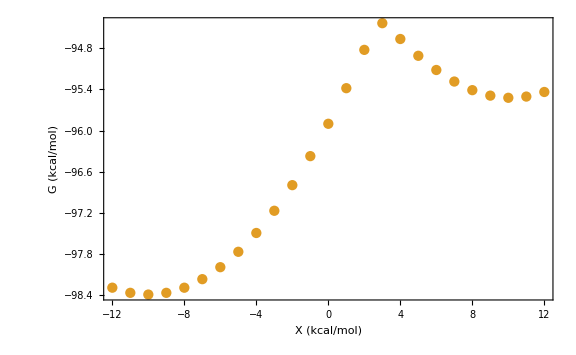

```mathematica
ListPlot[GS1DFESCauchy1Aa,Frame->True,FrameLabel->{"X (kcal/mol)","G (kcal/mol)"},FrameStyle->Black,LabelStyle->Large,ImageSize->Large]
```

```mathematica
GS1DFESCauchyMod1Aa=GS1DFESCauchyFixedRMod[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkA1,λA,ΔsA1,ϵcA,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,xAA,χsA,WxminHA,zH3O,xCL,kharA,RA,-1.0,offset,0.02,10,M->mH,DiffOrder->4]//Timing
```

{3.43248,{{-12,-95.4224},{-11,-95.4974},{-10,-95.5225},{-9,-95.4976},{-8,-95.4228},{-7,-95.298},{-6,-95.1232},{-5,-94.8986},{-4,-94.6241},{-3,-94.2999},{-2,-93.9261},{-1,-93.5027},{0,-93.0306},{1,-92.511},{2,-91.952},{3,-91.5625},{4,-91.7934},{5,-92.0384},{6,-92.2457},{7,-92.4142},{8,-92.5399},{9,-92.6199},{10,-92.6514},{11,-92.6335},{12,-92.5665}}}

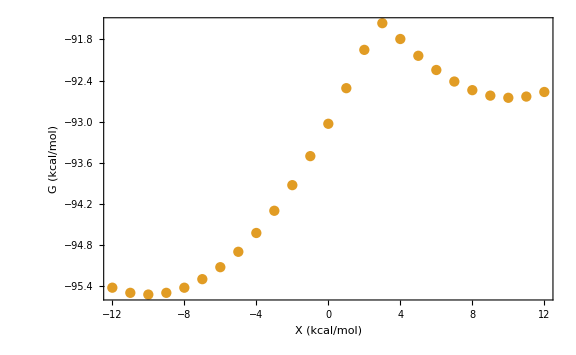

```mathematica
ListPlot[GS1DFESCauchyMod1Aa,Frame->True,FrameLabel->{"X (kcal/mol)","G (kcal/mol)"},FrameStyle->Black,LabelStyle->Large,ImageSize->Large]
```

```mathematica
GS1DFESCauchyMod1Ba=GS1DFESCauchyFixedRMod[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkA1,λA,ΔsA1,ϵcA,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,RB,χsA,WxminHA,zH3O,xCL,kharA,RB,-1.0,offset,0.02,10,M->mH,DiffOrder->4]//Timing
```

Gmin (kcal/mol) = -96.4552

10 lowest eigenvalues (kcal/mol) = {-93.8032,-88.7184,-83.8241,-79.8326,-79.8326,-73.2429,-73.8375,-73.8375,-67.1252,-67.1252}

Gmin (kcal/mol) = -96.5302

10 lowest eigenvalues (kcal/mol) = {-93.8782,-88.7934,-83.8991,-79.9076,-79.9076,-73.3179,-73.9125,-73.9125,-67.2002,-67.2002}

Gmin (kcal/mol) = -96.5552

10 lowest eigenvalues (kcal/mol) = {-93.9032,-88.8184,-83.9241,-79.9326,-79.9326,-73.3429,-73.9375,-73.9375,-67.2252,-67.2252}

Gmin (kcal/mol) = -96.5302

10 lowest eigenvalues (kcal/mol) = {-93.8782,-88.7934,-83.8991,-79.9076,-79.9076,-73.3179,-73.9125,-73.9125,-67.2002,-67.2002}

Gmin (kcal/mol) = -96.4552

10 lowest eigenvalues (kcal/mol) = {-93.8032,-88.7184,-83.8241,-79.8326,-79.8326,-73.2429,-73.8375,-73.8375,-67.1252,-67.1252}

Gmin (kcal/mol) = -96.3302

10 lowest eigenvalues (kcal/mol) = {-93.6816,-88.6199,-83.7364,-79.7006,-79.7006,-73.1736,-73.7057,-73.7057,-67.0068,-67.0068}

Gmin (kcal/mol) = -96.1552

10 lowest eigenvalues (kcal/mol) = {-93.5275,-88.5914,-83.7407,-79.4988,-79.4988,-73.2516,-73.505,-73.505,-66.8605,-66.8605}

Gmin (kcal/mol) = -95.9302

10 lowest eigenvalues (kcal/mol) = {-93.3433,-88.6132,-83.7567,-79.2507,-79.2507,-73.3415,-73.2575,-73.2575,-66.671,-66.671}

Gmin (kcal/mol) = -95.6552

10 lowest eigenvalues (kcal/mol) = {-93.1333,-88.6704,-83.742,-78.9658,-78.9658,-73.3832,-72.977,-72.977,-66.4344,-66.4344}

Gmin (kcal/mol) = -95.3302

10 lowest eigenvalues (kcal/mol) = {-92.9129,-88.76,-83.6706,-78.6464,-78.6464,-73.3639,-72.66,-72.66,-66.1535,-66.1535}

Gmin (kcal/mol) = -94.9552

10 lowest eigenvalues (kcal/mol) = {-92.6969,-88.8462,-83.5373,-78.2871,-78.2871,-73.2935,-72.3058,-72.3058,-65.832,-65.832}

Gmin (kcal/mol) = -94.8062

10 lowest eigenvalues (kcal/mol) = {-92.5027,-88.9021,-83.3614,-77.8862,-77.8862,-73.1813,-71.9267,-71.9267,-65.4691,-65.4691}

Gmin (kcal/mol) = -95.3208

10 lowest eigenvalues (kcal/mol) = {-92.3719,-88.8819,-83.1431,-77.4244,-77.4244,-73.0718,-71.4964,-71.4964,-65.0706,-65.0706}

Gmin (kcal/mol) = -95.7867

10 lowest eigenvalues (kcal/mol) = {-92.3008,-88.7512,-82.8872,-76.8978,-76.8978,-72.9579,-71.0173,-71.0173,-64.6292,-64.6292}

Gmin (kcal/mol) = -96.2035

10 lowest eigenvalues (kcal/mol) = {-92.3221,-88.5075,-82.6479,-76.3067,-76.3067,-72.9072,-70.5095,-70.5095,-64.1485,-64.1485}

Gmin (kcal/mol) = -96.5712

10 lowest eigenvalues (kcal/mol) = {-92.3919,-88.1545,-82.3918,-75.6061,-75.6061,-72.9368,-69.95,-69.95,-63.6197,-63.6197}

Gmin (kcal/mol) = -96.8894

10 lowest eigenvalues (kcal/mol) = {-92.502,-87.719,-82.1364,-74.6717,-74.6717,-73.3055,-69.3383,-69.3383,-63.0378,-63.0378}

Gmin (kcal/mol) = -97.1582

10 lowest eigenvalues (kcal/mol) = {-92.6197,-87.2247,-81.8649,-74.71,-73.1475,-73.1475,-68.6762,-68.6762,-62.4019,-62.4019}

Gmin (kcal/mol) = -97.3774

10 lowest eigenvalues (kcal/mol) = {-92.732,-86.7061,-81.5974,-74.957,-72.1379,-72.1379,-68.0034,-68.0034,-61.7122,-61.7122}

Gmin (kcal/mol) = -97.5469

10 lowest eigenvalues (kcal/mol) = {-92.8283,-86.1873,-81.2902,-74.8336,-71.2505,-71.2505,-67.2858,-67.2858,-60.9656,-60.9656}

Gmin (kcal/mol) = -97.6668

10 lowest eigenvalues (kcal/mol) = {-92.8904,-85.6744,-80.9079,-74.5419,-70.3782,-70.3782,-66.5154,-66.5154,-60.1634,-60.1634}

Gmin (kcal/mol) = -97.737

10 lowest eigenvalues (kcal/mol) = {-92.9228,-85.2144,-80.4396,-74.1746,-69.4864,-69.4864,-65.6915,-65.6915,-59.3097,-59.3097}

Gmin (kcal/mol) = -97.7574

10 lowest eigenvalues (kcal/mol) = {-92.9112,-84.7731,-79.8757,-73.7277,-68.566,-68.566,-64.8134,-64.8134,-58.396,-58.396}

Gmin (kcal/mol) = -97.728

10 lowest eigenvalues (kcal/mol) = {-92.8632,-84.4143,-79.2974,-73.8634,-69.2205,-65.7052,-63.9527,-63.9527,-57.3218,-57.3218}

Gmin (kcal/mol) = -97.6488

10 lowest eigenvalues (kcal/mol) = {-92.7701,-84.0832,-78.7006,-74.0856,-69.2432,-63.6269,-63.0077,-63.0077,-56.1346,-56.1346}

{1.93871,{{-12,-93.8032},{-11,-93.8782},{-10,-93.9032},{-9,-93.8782},{-8,-93.8032},{-7,-93.6816},{-6,-93.5275},{-5,-93.3433},{-4,-93.1333},{-3,-92.9129},{-2,-92.6969},{-1,-92.5027},{0,-92.3719},{1,-92.3008},{2,-92.3221},{3,-92.3919},{4,-92.502},{5,-92.6197},{6,-92.732},{7,-92.8283},{8,-92.8904},{9,-92.9228},{10,-92.9112},{11,-92.8632},{12,-92.7701}}}

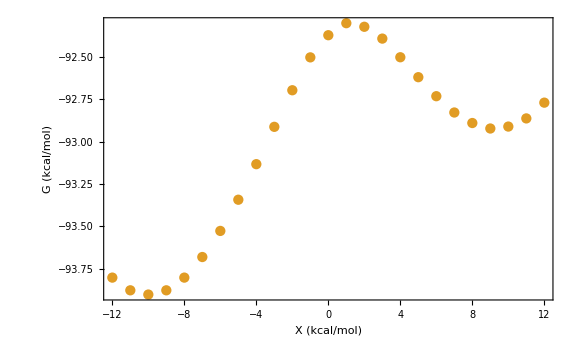

```mathematica
ListPlot[GS1DFESCauchyMod1Ba,Frame->True,FrameLabel->{"X (kcal/mol)","G (kcal/mol)"},FrameStyle->Black,LabelStyle->Large,ImageSize->Large]
```

```mathematica
GS2DFESCauchy1Aa=GS2DFESCauchy[DE1A,ω1A,DE2A,ω2A,rDH,rAH,WA,ΔkA1,λA,ΔsA1,ϵcA,γA,TT,xCL,xOHL,εCL,εw,c0ionsA,xAA,χsA,-1.0,0.02,5,0.1,zH3O,WxminHA,kharA,xCL,M->mH,DiffOrder->4]
```

{{{-12,2.7,-95.4273},{-12,2.8,-95.4224},{-12,2.9,-90.3267},{-12,3.,-95.4225},{-12,3.1,-95.4224},{-12,3.2,-95.4223},{-12,3.3,-95.4223},{-12,3.4,-95.4223},{-12,3.5,-95.4223},{-12,3.6,-95.4223}},{{-11,2.7,-95.5023},{-11,2.8,-95.4974},{-11,2.9,-90.4017},{-11,3.,-95.4978},{-11,3.1,-95.4974},{-11,3.2,-95.4973},{-11,3.3,-95.4973},{-11,3.4,-95.4973},{-11,3.5,-95.4973},{-11,3.6,-95.4973}},{{-10,2.7,-95.5273},{-10,2.8,-95.5224},{-10,2.9,-90.4267},{-10,3.,-95.5232},{-10,3.1,-95.5225},{-10,3.2,-95.5223},{-10,3.3,-95.5223},{-10,3.4,-95.5223},{-10,3.5,-95.5223},{-10,3.6,-95.5223}},{{-9,2.7,-95.5023},{-9,2.8,-95.4974},{-9,2.9,-90.4164},{-9,3.,-95.4987},{-9,3.1,-95.4976},{-9,3.2,-95.4973},{-9,3.3,-95.4973},{-9,3.4,-95.4973},{-9,3.5,-95.4973},{-9,3.6,-95.4973}},{{-8,2.7,-95.4273},{-8,2.8,-95.4224},{-8,2.9,-90.3832},{-8,3.,-95.4247},{-8,3.1,-95.4228},{-8,3.2,-95.4223},{-8,3.3,-95.4223},{-8,3.4,-95.4223},{-8,3.5,-95.4223},{-8,3.6,-95.4223}},{{-7,2.7,-95.3023},{-7,2.8,-95.2974},{-7,2.9,-90.3307},{-7,3.,-95.3009},{-7,3.1,-95.298},{-7,3.2,-95.2974},{-7,3.3,-95.2973},{-7,3.4,-95.2973},{-7,3.5,-95.2973},{-7,3.6,-95.2973}},{{-6,2.7,-95.1273},{-6,2.8,-95.1224},{-6,2.9,-90.2648},{-6,3.,-95.1278},{-6,3.1,-95.1232},{-6,3.2,-95.1224},{-6,3.3,-95.1223},{-6,3.4,-95.1223},{-6,3.5,-95.1223},{-6,3.6,-95.1223}},{{-5,2.7,-94.9023},{-5,2.8,-94.9031},{-5,2.9,-90.2074},{-5,3.,-94.9055},{-5,3.1,-94.8986},{-5,3.2,-94.8974},{-5,3.3,-94.8973},{-5,3.4,-94.8973},{-5,3.5,-94.8973},{-5,3.6,-94.8973}},{{-4,2.7,-94.6273},{-4,2.8,-94.6518},{-4,2.9,-90.1717},{-4,3.,-94.6342},{-4,3.1,-94.6241},{-4,3.2,-94.6225},{-4,3.3,-94.6223},{-4,3.4,-94.6223},{-4,3.5,-94.6223},{-4,3.6,-94.6223}},{{-3,2.7,-94.3023},{-3,2.8,-94.3717},{-3,2.9,-90.1798},{-3,3.,-94.315},{-3,3.1,-94.2999},{-3,3.2,-94.2976},{-3,3.3,-94.2973},{-3,3.4,-94.2973},{-3,3.5,-94.2973},{-3,3.6,-94.2973}},{{-2,2.7,-93.9279},{-2,2.8,-94.0683},{-2,2.9,-90.2366},{-2,3.,-93.9479},{-2,3.1,-93.9261},{-2,3.2,-93.9226},{-2,3.3,-93.9223},{-2,3.4,-93.9223},{-2,3.5,-93.9223},{-2,3.6,-93.9223}},{{-1,2.7,-93.5826},{-1,2.8,-93.753},{-1,2.9,-90.3468},{-1,3.,-93.5366},{-1,3.1,-93.5027},{-1,3.2,-93.4978},{-1,3.3,-93.4973},{-1,3.4,-93.4973},{-1,3.5,-93.4973},{-1,3.6,-93.4973}},{{0,2.7,-93.2964},{0,2.8,-93.4509},{0,2.9,-90.4681},{0,3.,-93.084},{0,3.1,-93.0306},{0,3.2,-93.023},{0,3.3,-93.0223},{0,3.4,-93.0223},{0,3.5,-93.0223},{0,3.6,-93.0223}},{{1,2.7,-93.0682},{1,2.8,-93.1695},{1,2.9,-90.5692},{1,3.,-92.6027},{1,3.1,-92.511},{1,3.2,-92.4984},{1,3.3,-92.4974},{1,3.4,-92.4973},{1,3.5,-92.4973},{1,3.6,-92.4973}},{{2,2.7,-92.9015},{2,2.8,-92.9614},{2,2.9,-90.5576},{2,3.,-92.1472},{2,3.1,-91.952},{2,3.2,-91.9245},{2,3.3,-91.9224},{2,3.4,-91.9223},{2,3.5,-91.9223},{2,3.6,-91.9223}},{{3,2.7,-92.7994},{3,2.8,-92.8095},{3,2.9,-90.3672},{3,3.,-91.911},{3,3.1,-91.5625},{3,3.2,-91.4185},{3,3.3,-91.4198},{3,3.4,-91.4549},{3,3.5,-91.4721},{3,3.6,-91.3579}},{{4,2.7,-92.7602},{4,2.8,-92.7543},{4,2.9,-92.3987},{4,3.,-91.9991},{4,3.1,-91.7934},{4,3.2,-91.7334},{4,3.3,-91.7557},{4,3.4,-91.7923},{4,3.5,-91.7137},{4,3.6,-91.6683}},{{5,2.7,-92.7552},{5,2.8,-92.7367},{5,2.9,-92.4557},{5,3.,-92.1781},{5,3.1,-92.0384},{5,3.2,-92.0137},{5,3.3,-92.0423},{5,3.4,-92.0779},{5,3.5,-91.9599},{5,3.6,-91.934}},{{6,2.7,-92.7772},{6,2.8,-92.7623},{6,2.9,-92.5466},{6,3.,-92.3443},{6,3.1,-92.2457},{6,3.2,-92.246},{6,3.3,-92.2785},{6,3.4,-92.2312},{6,3.5,-92.1703},{6,3.6,-92.1522}},{{7,2.7,-92.7981},{7,2.8,-87.2839},{7,2.9,-92.6235},{7,3.,-92.4824},{7,3.1,-92.4142},{7,3.2,-92.4296},{7,3.3,-92.4639},{7,3.4,-92.3686},{7,3.5,-92.336},{7,3.6,-92.3218}},{{8,2.7,-92.8136},{8,2.8,-86.6747},{8,2.9,-92.6856},{8,3.,-92.5808},{8,3.1,-92.5399},{8,3.2,-92.5644},{8,3.3,-92.5858},{8,3.4,-92.4763},{8,3.5,-92.4542},{8,3.6,-92.4423}},{{9,2.7,-92.8126},{9,2.8,-86.0629},{9,2.9,-92.7157},{9,3.,-92.6335},{9,3.1,-92.6199},{9,3.2,-92.6488},{9,3.3,-92.5906},{9,3.4,-92.5407},{9,3.5,-92.5237},{9,3.6,-92.5134}},{{10,2.7,-92.7771},{10,2.8,-85.4676},{10,2.9,-92.7052},{10,3.,-92.6429},{10,3.1,-92.6514},{10,3.2,-92.6823},{10,3.3,-92.5887},{10,3.4,-92.5583},{10,3.5,-92.5442},{10,3.6,-92.5349}},{{11,2.7,-92.7091},{11,2.8,-84.9198},{11,2.9,-92.6565},{11,3.,-92.6139},{11,3.1,-92.6335},{11,3.2,-92.658},{11,3.3,-92.5495},{11,3.4,-92.5274},{11,3.5,-92.5152},{11,3.6,-92.5068}},{{12,2.7,-92.6032},{12,2.8,-84.3949},{12,2.9,-92.561},{12,3.,-92.5398},{12,3.1,-92.5665},{12,3.2,-92.518},{12,3.3,-92.4652},{12,3.4,-92.4476},{12,3.5,-92.4367},{12,3.6,-92.4295}}}

```mathematica
GS2DFESCauchy1AaFlat=Flatten[GS2DFESCauchy1Aa,1];
```

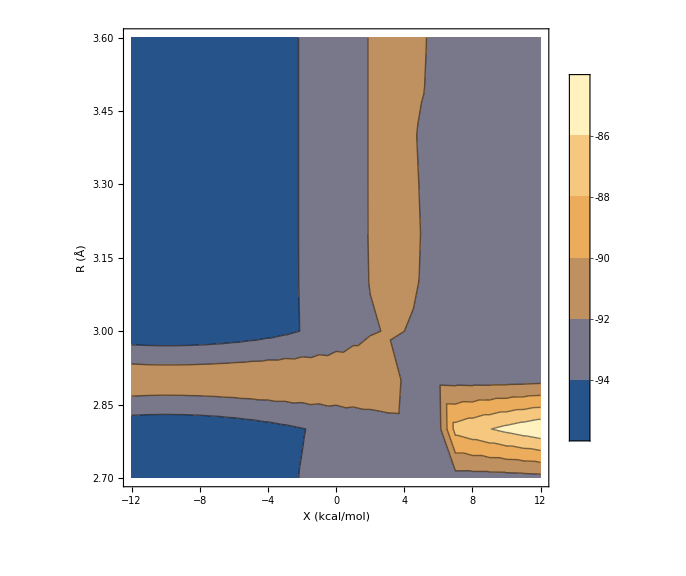

```mathematica
ListContourPlot[GS2DFESCauchy1AaFlat,PlotLegends->Automatic,Frame->True,FrameLabel->{"X (kcal/mol)","R (Å)"},FrameStyle->Black,LabelStyle->Large,ImageSize->Large]
```